```mathematica
ssubs0={g->980,σ->20,qx->0,qy->2*Pi/4,μ->0.005,ρ->1,h0->0.1,ω->0.5*ωd};
ssubs1={g->980,σ->20,qx->0,qy->2*Pi/4*0.95,μ->0.005,ρ->1,h0->0.1,ω->0.5*ωd};
hsubs1={g->980,σ->20,qx->0,qy->2*Pi/2*0.95,μ->0.005,ρ->1,h0->0.1,ω->0.000001*ωd};
ssubs2={g->980,σ->20,qx->0,qy->2*Pi/4*1.05,μ->0.005,ρ->1,h0->0.1,ω->0.5*ωd};
hsubs2={g->980,σ->20,qx->0,qy->2*Pi/2*1.05,μ->0.005,ρ->1,h0->0.1,ω->0.000001*ωd};

Ω1[l1_]:=((qx^2+qy^2)+I*ρ/μ*(ω+l1*ωd))^(1/2)
κ=(qx^2+qy^2)^(1/2);
mat1flat[l1_,l2_]:={{2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]+(2 (qy^2-κ^2) Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qx (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]-(2 qy^2 Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qy (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{4 ⅈ ⅇ^(-h0 Ω1[l1]) qx (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),4 ⅈ ⅇ^(-h0 Ω1[l1]) qy (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),1/(2 μ ρ (κ^2+Ω1[l1]^2))ⅇ^(-h0 (κ+Ω1[l1])) (-4 ⅇ^(h0 κ) κ^4 μ^2+ⅇ^(h0 Ω1[l1]) κ (κ^3 μ^2-g ρ^2-κ^2 ρ σ)+ⅇ^(h0 (2 κ+Ω1[l1])) κ (κ^3 μ^2+g ρ^2+κ^2 ρ σ)-4 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^3 μ^2 Ω1[l1]+2 (-2 ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^2 μ^2 Ω1[l1]^2+ⅇ^(h0 Ω1[l1]) (1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)}}*KroneckerDelta[l1,l2]
mat2flat[l1_,l2_]:={{0,0,-(ⅈ qx ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,-(ⅈ qy ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,(κ ρ (-1+l1,l2+1+l1,l2) Sinh[h0 κ])/(2 μ (κ^2+Ω1[l1]^2))}}

mat1[n1_,n2_,m1_,m2_,l1_,l2_]:={{C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κx[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κy[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{ⅈ μ κx[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),ⅈ μ κy[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),1/2 (C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+κ1[n1,m1] (2 μ (-C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2]) κ1[n1,m1]+(S1[m1,m2,n1,n2] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))}} l1,l2
mat2[n1_,n2_,m1_,m2_,l1_,l2_]:=-{{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,(ρ^2 S1[m1,m2,n1,n2] κ1[n1,m1])/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))}} (-1/2 (-1+l1,l2+1+l1,l2))
```

### symbolic inversion

```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A/ρ*kx/ω*Exp[k*z]-B/ρ*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A/ρ*ky/ω*Exp[k*z]-B/ρ*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A/ρ*k/ω*Exp[k*z]-I*B/ρ*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=-ρ*g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
subs1={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2]};
subs2={kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) kx)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) ky)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω)+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))-g z ρ

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]/ρ]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]/ρ]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]/ρ+g]
```

0

0

0

```mathematica
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs1/.subs2],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs1/.subs2],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,4]*I2m[l1,m1,m2,n1,n2])-kx/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,6]*I2m[l1,m1,m2,n1,n2])-ky/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,8]*I2m[l1,m1,m2,n1,n2])+I*k/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]-KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2]},{k1,1,9}]];
```

```mathematica
elim=Range[6];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Expand[Det[eqs1[[elim,perts[[i]]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;Abs[u]≠0.]]
ipert=lperts[[7]]
First/@subs1[[Complement[Range[9],perts[[ipert]]]]]
```

{2,3,4,5,7,8,9,10,11,12,13,14,18,19,20,21,24,25,26,27}

9

{Bx,By,H}

```mathematica
mat=FullSimplify[Expand[FullSimplify[Simplify[eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]/.m2->m1/.n2->n1/.l2->l1].(eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.m2->m1/.n2->n1/.l2->l1)/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ(ρ/μ*Ω1[n1,m1,l1]-κx^2-κy^2)-l1 ωd/.κx^2->κ1[n1,m1]^2-κy^2,κ1[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ1[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l2->l1].DiagonalMatrix[{ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ρ}]]/.I2m[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2])/2/ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))/.I2p[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2])/2/ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))/.I1m[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]+S1[m1,m2,n1,n2])/2/ⅇ^(h0 κ1[n1,m1])/.I1p[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]-S1[m1,m2,n1,n2])/2/ⅇ^(-h0 κ1[n1,m1])]/.-κ1[n1,m1]^2+κy[n1,m1]^2->-κx[n1,m2]^2;
MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]
```

(C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κx[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κx[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κy[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κy[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
(ⅈ S2[l1,m1,m2,n1,n2] κx[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | (ⅈ S2[l1,m1,m2,n1,n2] κy[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -μ C2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+μ S2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+1/2 C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+(S1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))

```mathematica
Simplify[Normal[Series[mat/.Ω1[n1,m1,l1]->I*(ω+l1*ωd)+μ/ρ*(κx^2+κy^2),{μ,0,0}]]]
```

{{C2[l1,m1,m2,n1,n2],0,(((ρ (ω+l1 ωd)^2 S1[m1,m2,n1,n2])/κ1[n1,m1]-C1[m1,m2,n1,n2] (g ρ+σ κ1[n1,m1]^2)) κx[n1,m1])/(2 (ω+l1 ωd))},{0,C2[l1,m1,m2,n1,n2],(((ρ (ω+l1 ωd)^2 S1[m1,m2,n1,n2])/κ1[n1,m1]-C1[m1,m2,n1,n2] (g ρ+σ κ1[n1,m1]^2)) κy[n1,m1])/(2 (ω+l1 ωd))},{0,0,(ⅈ (ρ (ω+l1 ωd)^2 C1[m1,m2,n1,n2]-S1[m1,m2,n1,n2] κ1[n1,m1] (g ρ+σ κ1[n1,m1]^2)))/(2 (ω+l1 ωd))}}

```mathematica
FullSimplify[MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]/.κ[n1,m1]->Subscript[κ,m n]/.Ω1[n1,m1,l1]->Subscript["Ω",l m n]/.κx[n1,m1]->Subscript[κx,m n]/.κy[n1,m1]->Subscript[κy,m n]/.C1[m1,m2,n1,n2]->Subsuperscript[C1,m'n',m n]/.S1[m1,m2,n1,n2]->Subsuperscript[S1,m' n',m n]/.C2[l1,m1,m2,n1,n2]->Subsuperscript[C2,l'm'n',l m n]/.S2[l1,m1,m2,n1,n2]->Subsuperscript[S2,l'm'n',l m n]]
```

(C2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κx[n1,m2]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κx_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
-(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | C2_(l' m' n')^(l m n)-(2 μ κy_(m n)^2 C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κy_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
ⅈ κx_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | ⅈ κy_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | 1/2 (ρ Ω_(l m n) C1_(m' n')^(m n)+κ1[n1,m1] (μ (C1_(m' n')^(m n)-2 C2_(l' m' n')^(l m n)+2 S2_(l' m' n')^(l m n)) κ1[n1,m1]+(S1_(m' n')^(m n) (g ρ^2+(ρ σ-4 μ^2 √((ρ Ω_(l m n))/μ)) κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2))))

### flat substrate

```mathematica
C1[m1_,m2_,n1_,n2_]:=ⅇ^(- h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]+ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]]
```

```mathematica
M=5;
Clear[ω]
Clear[ωd]
Clear[qx]
Clear[qy]
Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]
```

{0.133263,Null}

{0.017435,Null}

```mathematica
((qx^2+qy^2)^(1/2)*Tanh[(qx^2+qy^2)^(1/2)*h0]*(g+σ/ρ*(qx^2+qy^2)))^(1/2)/(2*Pi)/.ssubs0
```

2.52607

```mathematica
freq=2*Pi*5;

{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.ssubs0/.ωd->freq];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.ssubs0/.ωd->freq];
evalsbase
evalsbase2
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-189956.+1897.72 ⅈ,189956.-1897.72 ⅈ,-88972.2+421.106 ⅈ,88972.2-421.106 ⅈ,43113.7-9.09588 ⅈ,-43113.7+9.09588 ⅈ,13789.6-0.00108577 ⅈ,-13789.6+0.00108577 ⅈ,379.552-2.95686×10^-14 ⅈ,-379.552-3.02127×10^-12 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-6.42645×10^17+6.90188×10^16 ⅈ,5.32495×10^17+2.68941×10^16 ⅈ,4.90008×10^17-1.55911×10^17 ⅈ,4.24692×10^17+3.37828×10^16 ⅈ,189956.+1897.72 ⅈ,-189956.-1897.72 ⅈ,88972.2+421.106 ⅈ,-88972.2-421.106 ⅈ,-43113.7-9.09588 ⅈ,43113.7+9.09588 ⅈ,13789.6+0.00108577 ⅈ,-13789.6-0.00108577 ⅈ,379.552-1.32827×10^-11 ⅈ,-379.552+1.40778×10^-11 ⅈ}

```mathematica
ω0=2*Pi*2;
ω1=2*Pi*10;
num=100;
freqs=Table[freq,{freq,ω0,ω1,(ω1-ω0)/num}];
AbsoluteTiming[Monitor[subharmonic=Table[Eigenvalues[{eq1base,eq2base}/.ssubs1/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic=Table[Eigenvalues[{eq1base,eq2base}/.hsubs1/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[subharmonic2=Table[Eigenvalues[{eq1base,eq2base}/.ssubs2/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic2=Table[Eigenvalues[{eq1base,eq2base}/.hsubs2/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
```

{1.2814,Null}

{1.2427,Null}

{1.28596,Null}

{1.25831,Null}

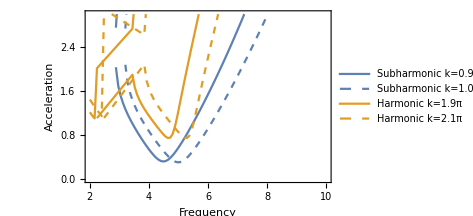

```mathematica
p=Legended[Show[ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic])/980)),{}]],PlotRange->{{2,10},{0,3}},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Dashed]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Dashed]}],ImageSize->350],LineLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[2]],Dashed]},{"Subharmonic k=0.95π","Subharmonic k=1.05π","Harmonic k=1.9π","Harmonic k=2.1π"}]]
```

### periodic

```mathematica
S1[m1_,m2_,n1_,n2_]:=-(ⅇ^(-h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]-ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]])
C2[l1_,m1_,m2_,n1_,n2_]:=ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]+ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]
S2[l1_,m1_,m2_,n1_,n2_]:=-(ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]-ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)])
κx[n1_,m1_]:=qx+n1*q1.{1,0}+m1*q2.{1,0}
κy[n1_,m1_]:=qy+n1*q1.{0,1}+m1*q2.{0,1}
κ1[n1_,m1_]:=(κx[n1,m1]^2+κy[n1,m1]^2)^(1/2)
Ω1[n1_,m1_,l1_]:=μ/ρ*(I*ρ/μ*(ω+l1*ωd)+κ1[n1,m1]^2)
```

```mathematica
BesselI[1,{{1},{2},{3}}]
```

{{BesselI[1,1]},{BesselI[1,2]},{BesselI[1,3]}}

```mathematica
FullSimplify[TrigToExp[((mat1[0,0,0,0,l1,l2]/.as->0)-(mat1flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}]))],ρ>0&&μ>0]
FullSimplify[TrigToExp[((mat2[0,0,0,0,l1,l2]/.as->0)-(mat2flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}]))],ρ>0&&μ>0]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
M=3;
M2=3;
ks=2*Pi;

Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]

freq=2*Pi*5;
ks=2*Pi/2;
subs={q1->ks*{3.^(1/2)/2,-1/2},q2->ks*{0,1}};

{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs0/.ωd->freq];
{evalsbase2,evecsbase2}=Eigensystem[{Transpose[eq1base],Transpose[eq2base]}/.subs/.ssubs0/.ωd->freq];

ord1=OrderingBy[evalsbase,Abs[Im[#]]&][[1;;2]];
ord2=OrderingBy[evalsbase2,Abs[Im[#]]&][[1;;2]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}


Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs0/.ωd->freq/.as->0.01],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs0/.ωd->freq/.as->0.01],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];

w=lev[[All,ind1]];
v=rev[[All,ind2]];
(w.eq1.v)/(w.eq2.v)
```

{0.057565,Null}

{0.010175,Null}

{379.552-1.78728×10^-8 ⅈ,379.552-1.78696×10^-8 ⅈ}

{295.477,Null}

{43.101,Null}

379.552-1.78712×10^-8 ⅈ

```mathematica
(*Add the predictor stage, δλ = δa w.(dT/da).v/( w.(dT/dλ).v ) and T.δv = -(δa dT/da + δλ dT/dλ).v and Transpose[T].δw = -Transpose[δa dT/da + δλ dT/dλ].v. We will need the matrix derivatives...*)
```

```mathematica
ws={};
vs={};
λs={};
w=lev[[All,ind1]];
v=rev[[All,ind2]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=w.eq1.v/(w.eq2.v);
v=LinearSolve[(λ*eq2-eq1),eq2.v,Method->"Multifrontal"];
w=LinearSolve[Transpose[(λ*eq2-eq1)],Transpose[eq2].w,Method->"Multifrontal"];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[(eq1-λ*eq2).v]," ", Norm[Transpose[eq1-λ*eq2].w]];
,{k,1,10}]]
```

1 379.552-1.78712×10^-8 ⅈ 0.9145 0.431753

2 369.95+7.21664×10^-7 ⅈ 0.65611 0.316665

3 348.938+9.19379×10^-7 ⅈ 0.138586 0.0682459

4 342.451-8.12683×10^-8 ⅈ 0.00082464 0.000407745

5 342.41-1.02505×10^-7 ⅈ 1.56633×10^-10 7.7452×10^-11

6 342.41-1.02505×10^-7 ⅈ 2.6318×10^-14 2.82732×10^-15

7 342.41-1.02505×10^-7 ⅈ 2.42245×10^-14 4.09355×10^-15

8 342.41-1.02505×10^-7 ⅈ 2.02235×10^-14 3.19255×10^-15

9 342.41-1.02505×10^-7 ⅈ 2.24985×10^-14 3.08262×10^-15

10 342.41-1.02505×10^-7 ⅈ 2.88552×10^-14 2.99612×10^-15

{20.465,Null}

### continuation

```mathematica
asmax=0.05;
das=0.005;
freqmin=2*Pi*2;
freqmax=2*Pi*10;
freq0=2*Pi*5;
dfreq=Pi;
```

#### subharmonic

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs1/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Transpose[eq1base],Transpose[eq2base]}/.subs/.ssubs1/.ωd->freq0];

ord1=OrderingBy[evalsbase,Abs[Im[#]]&][[1;;2]];
ord2=OrderingBy[evalsbase2,Abs[Im[#]]&][[1;;2]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}
rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{565.837-9.80556×10^-8 ⅈ,565.837-9.80669×10^-8 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{179.882,Null}

{25.2095,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
v=rev[[All,ind1]];
w=lev[[All,ind2]];
AbsoluteTiming[Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[
λ=w.test1.v/(w.test2.v);
v=LinearSolve[(λ*test2-test1),test2.v,Method->"Multifrontal"];
w=LinearSolve[Transpose[(λ*test2-test1)],Transpose[test2].w,Method->"Multifrontal"];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Transpose[test1-λ*test2].w]];
AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
,{k,1,10}]]
,{As,das,asmax,das}]]
```

{18.478,Null}{3.03895,Null}

1 565.837-9.80554×10^-8 ⅈ 0.0899292 0.0386391

2 570.141-4.07985×10^-6 ⅈ 0.0000102337 4.36667×10^-6

3 570.141-4.0797×10^-6 ⅈ 1.94679×10^-14 6.17758×10^-15

4 570.141-4.0797×10^-6 ⅈ 2.70351×10^-14 4.01987×10^-15

5 570.141-4.0797×10^-6 ⅈ 1.16571×10^-14 3.11818×10^-15

6 570.141-4.0797×10^-6 ⅈ 2.46818×10^-14 3.79666×10^-15

7 570.141-4.0797×10^-6 ⅈ 2.35706×10^-14 4.25275×10^-15

8 570.141-4.0797×10^-6 ⅈ 2.38289×10^-14 5.00585×10^-15

9 570.141-4.0797×10^-6 ⅈ 1.84824×10^-14 3.14289×10^-15

10 570.141-4.0797×10^-6 ⅈ 1.43348×10^-14 5.2285×10^-15

{19.3248,Null}{2.94642,Null}

1 578.784-0.0000128722 ⅈ 0.0857345 0.0383247

2 583.066-0.0000185897 ⅈ 8.58503×10^-6 3.76789×10^-6

3 583.066-0.0000185897 ⅈ 2.83594×10^-14 6.53342×10^-15

4 583.066-0.0000185897 ⅈ 3.86174×10^-14 5.27553×10^-15

5 583.066-0.0000185897 ⅈ 4.50064×10^-14 5.02345×10^-15

6 583.066-0.0000185897 ⅈ 3.7951×10^-14 5.87895×10^-15

7 583.066-0.0000185897 ⅈ 1.61792×10^-14 9.42923×10^-15

8 583.066-0.0000185897 ⅈ 3.42244×10^-14 3.85224×10^-15

9 583.066-0.0000185897 ⅈ 2.72014×10^-14 8.99349×10^-15

10 583.066-0.0000185897 ⅈ 5.17293×10^-14 5.92691×10^-15

{19.7873,Null}{2.9672,Null}

1 600.445-0.000042825 ⅈ 0.0789971 0.0376299

2 604.677-0.0000536566 ⅈ 6.25916×10^-6 2.89597×10^-6

3 604.678-0.0000536571 ⅈ 2.84589×10^-14 5.93649×10^-15

4 604.678-0.0000536571 ⅈ 3.48978×10^-14 8.05104×10^-15

5 604.678-0.0000536571 ⅈ 3.81218×10^-14 4.54037×10^-15

6 604.678-0.0000536571 ⅈ 2.30458×10^-14 5.437×10^-15

7 604.678-0.0000536571 ⅈ 2.26021×10^-14 4.20291×10^-15

8 604.678-0.0000536571 ⅈ 2.44881×10^-14 5.70507×10^-15

9 604.678-0.0000536571 ⅈ 2.97447×10^-14 6.45707×10^-15

10 604.678-0.0000536571 ⅈ 2.68266×10^-14 5.87543×10^-15

{19.7394,Null}{2.79616,Null}

1 630.97-0.000111742 ⅈ 0.0706336 0.0369527

2 635.17-0.000136711 ⅈ 4.14205×10^-6 2.08317×10^-6

3 635.17-0.000136713 ⅈ 3.45821×10^-14 4.66887×10^-15

4 635.17-0.000136713 ⅈ 3.25617×10^-14 4.16166×10^-15

5 635.17-0.000136713 ⅈ 3.26857×10^-14 4.17934×10^-15

6 635.17-0.000136713 ⅈ 2.3857×10^-14 7.67544×10^-15

7 635.17-0.000136713 ⅈ 2.11422×10^-14 5.63339×10^-15

8 635.17-0.000136713 ⅈ 3.19081×10^-14 7.3192×10^-15

9 635.17-0.000136713 ⅈ 2.57422×10^-14 6.22934×10^-15

10 635.17-0.000136713 ⅈ 2.70049×10^-14 4.18834×10^-15

{21.1246,Null}{3.2227,Null}

1 670.73-0.000277626 ⅈ 0.0616068 0.036657

2 674.952-0.000343506 ⅈ 2.60528×10^-6 1.47462×10^-6

3 674.952-0.000343514 ⅈ 3.65597×10^-14 7.14105×10^-15

4 674.952-0.000343514 ⅈ 3.54545×10^-14 6.74116×10^-15

5 674.952-0.000343514 ⅈ 3.53084×10^-14 5.75096×10^-15

6 674.952-0.000343514 ⅈ 3.18788×10^-14 7.64139×10^-15

7 674.952-0.000343514 ⅈ 4.44293×10^-14 7.52364×10^-15

8 674.952-0.000343514 ⅈ 3.53903×10^-14 5.0378×10^-15

9 674.952-0.000343514 ⅈ 3.62377×10^-14 5.9231×10^-15

10 674.952-0.000343514 ⅈ 3.23417×10^-14 7.69345×10^-15

{22.2496,Null}{2.92157,Null}

1 720.396-0.000704448 ⅈ 0.05274 0.0369835

2 724.726-0.000895834 ⅈ 1.62046×10^-6 1.06822×10^-6

3 724.727-0.000895859 ⅈ 4.31431×10^-14 5.87629×10^-15

4 724.727-0.000895859 ⅈ 5.29745×10^-14 7.5694×10^-15

5 724.727-0.000895859 ⅈ 5.54682×10^-14 6.33221×10^-15

6 724.727-0.000895859 ⅈ 3.41004×10^-14 6.48981×10^-15

7 724.727-0.000895859 ⅈ 4.11705×10^-14 8.15343×10^-15

8 724.727-0.000895859 ⅈ 4.65463×10^-14 6.09934×10^-15

9 724.727-0.000895859 ⅈ 3.78938×10^-14 9.56527×10^-15

10 724.727-0.000895859 ⅈ 4.15599×10^-14 7.12191×10^-15

{20.8378,Null}{2.90177,Null}

1 781.018-0.00188645 ⅈ 0.0446443 0.0380597

2 785.562-0.00247877 ⅈ 1.02772×10^-6 8.11253×10^-7

3 785.562-0.00247885 ⅈ 4.53404×10^-14 7.72811×10^-15

4 785.562-0.00247885 ⅈ 5.18226×10^-14 8.67775×10^-15

5 785.562-0.00247885 ⅈ 5.16968×10^-14 8.97768×10^-15

6 785.562-0.00247885 ⅈ 5.17548×10^-14 9.42914×10^-15

7 785.562-0.00247885 ⅈ 5.12001×10^-14 9.92687×10^-15

8 785.562-0.00247885 ⅈ 4.83701×10^-14 9.12434×10^-15

9 785.562-0.00247885 ⅈ 4.85676×10^-14 8.7796×10^-15

10 785.562-0.00247885 ⅈ 4.81776×10^-14 1.1571×10^-14

{20.6077,Null}{2.84212,Null}

1 854.097-0.0053783 ⅈ 0.0376872 0.0399209

2 858.971-0.00729958 ⅈ 6.77765×10^-7 6.48901×10^-7

3 858.971-0.00730008 ⅈ 6.57858×10^-14 1.12907×10^-14

4 858.971-0.00730008 ⅈ 6.11783×10^-14 1.18782×10^-14

5 858.971-0.00730008 ⅈ 6.48599×10^-14 1.10758×10^-14

6 858.971-0.00730008 ⅈ 6.24217×10^-14 1.09469×10^-14

7 858.971-0.00730008 ⅈ 6.38899×10^-14 1.36412×10^-14

8 858.971-0.00730008 ⅈ 6.4727×10^-14 1.34999×10^-14

9 858.971-0.00730008 ⅈ 6.59999×10^-14 1.29136×10^-14

10 858.971-0.00730008 ⅈ 6.38061×10^-14 1.18209×10^-14

{21.836,Null}{2.93457,Null}

1 941.679-0.016412 ⅈ 0.0320455 0.0424345

2 946.99-0.0249234 ⅈ 4.52311×10^-7 5.10829×10^-7

3 946.99-0.0249298 ⅈ 1.05842×10^-13 2.23788×10^-14

4 946.99-0.0249298 ⅈ 1.06815×10^-13 2.37901×10^-14

5 946.99-0.0249298 ⅈ 1.07238×10^-13 2.19938×10^-14

6 946.99-0.0249298 ⅈ 1.10306×10^-13 2.14916×10^-14

7 946.99-0.0249298 ⅈ 1.06147×10^-13 2.12594×10^-14

8 946.99-0.0249298 ⅈ 1.13312×10^-13 2.3548×10^-14

9 946.99-0.0249298 ⅈ 1.12167×10^-13 2.16704×10^-14

10 946.99-0.0249298 ⅈ 1.03285×10^-13 2.42453×10^-14

{20.8968,Null}{2.83575,Null}

1 1046.42-0.0633589 ⅈ 0.0279924 0.0448282

2 1052.18-0.144897 ⅈ 2.63103×10^-6 2.68669×10^-6

3 1052.18-0.145247 ⅈ 4.61431×10^-13 5.95997×10^-14

4 1052.18-0.145247 ⅈ 4.14519×10^-13 6.02474×10^-14

5 1052.18-0.145247 ⅈ 4.38641×10^-13 5.52469×10^-14

6 1052.18-0.145247 ⅈ 4.42877×10^-13 5.22898×10^-14

7 1052.18-0.145247 ⅈ 4.56303×10^-13 6.49009×10^-14

8 1052.18-0.145247 ⅈ 4.81688×10^-13 5.92471×10^-14

9 1052.18-0.145247 ⅈ 4.58642×10^-13 5.15946×10^-14

10 1052.18-0.145247 ⅈ 4.38583×10^-13 6.21152×10^-14

{509.259,Null}

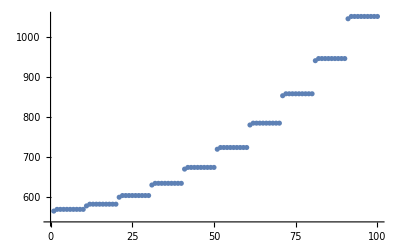

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λps={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ 
λ=w.test1.v/(w.test2.v);
v=LinearSolve[(λ*test2-test1),test2.v,Method->"Multifrontal"];
w=LinearSolve[Transpose[(λ*test2-test1)],Transpose[test2].w,Method->"Multifrontal"];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Transpose[test1-λ*test2].w]];
AppendTo[λps,λ];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{21.0615,Null}{2.81775,Null}

1 1052.18-0.145247 ⅈ 4.55922×10^-13 5.35365×10^-14

2 1052.18-0.145247 ⅈ 4.64532×10^-13 5.02033×10^-14

3 1052.18-0.145247 ⅈ 4.61226×10^-13 4.88061×10^-14

4 1052.18-0.145247 ⅈ 4.74833×10^-13 5.96191×10^-14

5 1052.18-0.145247 ⅈ 4.67066×10^-13 5.30085×10^-14

6 1052.18-0.145247 ⅈ 4.35353×10^-13 5.79057×10^-14

7 1052.18-0.145247 ⅈ 4.58708×10^-13 5.27777×10^-14

8 1052.18-0.145247 ⅈ 4.47707×10^-13 5.59003×10^-14

9 1052.18-0.145247 ⅈ 4.45105×10^-13 5.04184×10^-14

10 1052.18-0.145247 ⅈ 4.54921×10^-13 6.17692×10^-14

{21.056,Null}{2.82568,Null}

1 1555.38-1.83306 ⅈ 0.110247 0.108371

2 1543.62-0.0669189 ⅈ 0.00421673 0.00791955

3 1543.07+0.308535 ⅈ 8.03585×10^-7 1.29307×10^-6

4 1543.07+0.308647 ⅈ 5.54364×10^-13 2.04778×10^-12

5 1543.07+0.308647 ⅈ 5.8471×10^-13 2.23958×10^-12

6 1543.07+0.308647 ⅈ 5.76079×10^-13 2.03678×10^-12

7 1543.07+0.308647 ⅈ 6.28775×10^-13 2.08708×10^-12

8 1543.07+0.308647 ⅈ 6.44302×10^-13 2.08445×10^-12

9 1543.07+0.308647 ⅈ 5.77095×10^-13 2.14829×10^-12

10 1543.07+0.308647 ⅈ 5.40312×10^-13 1.91745×10^-12

{20.9532,Null}{2.83197,Null}

1 1857.72+7.09363 ⅈ 2.05156 3.69489

2 2070.29+7.6927 ⅈ 1.17306 1.0487

3 2200.24+1.02669 ⅈ 0.0241441 0.0340302

4 2205.34-0.149674 ⅈ 1.02452×10^-6 1.32611×10^-6

5 2205.34-0.149666 ⅈ 6.77352×10^-13 7.13081×10^-13

6 2205.34-0.149666 ⅈ 6.09732×10^-13 7.89508×10^-13

7 2205.34-0.149666 ⅈ 6.72963×10^-13 8.36809×10^-13

8 2205.34-0.149666 ⅈ 6.64755×10^-13 8.29372×10^-13

9 2205.34-0.149666 ⅈ 6.91458×10^-13 6.60632×10^-13

10 2205.34-0.149666 ⅈ 6.0836×10^-13 6.43227×10^-13

{21.5165,Null}{2.95365,Null}

1 2826.05-0.705709 ⅈ 0.0970018 0.115684

2 2845.65+0.728944 ⅈ 0.000167534 0.000135513

3 2845.66+0.749038 ⅈ 2.45895×10^-11 2.05567×10^-11

4 2845.66+0.749038 ⅈ 5.32519×10^-12 2.92618×10^-12

5 2845.66+0.749038 ⅈ 5.87723×10^-12 4.5177×10^-12

6 2845.66+0.749038 ⅈ 5.58172×10^-12 5.2492×10^-12

7 2845.66+0.749038 ⅈ 5.04988×10^-12 4.23002×10^-12

8 2845.66+0.749038 ⅈ 6.22383×10^-12 5.2326×10^-12

9 2845.66+0.749038 ⅈ 5.686×10^-12 4.24844×10^-12

10 2845.66+0.749038 ⅈ 5.28068×10^-12 3.16448×10^-12

{21.4096,Null}{2.98627,Null}

1 3542.16+3.39977 ⅈ 0.0397398 0.0314344

2 3546.25-0.159248 ⅈ 0.0000118115 0.0000126725

3 3546.25-0.157023 ⅈ 3.63899×10^-12 4.57313×10^-12

4 3546.25-0.157023 ⅈ 3.70032×10^-12 3.63381×10^-12

5 3546.25-0.157023 ⅈ 3.84626×10^-12 3.83115×10^-12

6 3546.25-0.157023 ⅈ 3.98058×10^-12 3.38637×10^-12

7 3546.25-0.157023 ⅈ 4.15176×10^-12 4.28492×10^-12

8 3546.25-0.157023 ⅈ 3.76819×10^-12 4.59348×10^-12

9 3546.25-0.157023 ⅈ 3.78642×10^-12 4.27941×10^-12

10 3546.25-0.157023 ⅈ 4.27276×10^-12 3.31846×10^-12

{22.1589,Null}{3.15212,Null}

1 4283.95-4.86638 ⅈ 0.0668068 0.0683436

2 4296.09+0.15071 ⅈ 0.0000513302 0.0000532072

3 4296.09+0.141247 ⅈ 1.08265×10^-11 9.97097×10^-12

4 4296.09+0.141247 ⅈ 7.70774×10^-12 4.50362×10^-12

5 4296.09+0.141247 ⅈ 7.23373×10^-12 5.69169×10^-12

6 4296.09+0.141247 ⅈ 7.98175×10^-12 4.33165×10^-12

7 4296.09+0.141247 ⅈ 6.7482×10^-12 5.68051×10^-12

8 4296.09+0.141247 ⅈ 6.93598×10^-12 5.72491×10^-12

9 4296.09+0.141247 ⅈ 7.31925×10^-12 4.09612×10^-12

10 4296.09+0.141247 ⅈ 6.54809×10^-12 5.34385×10^-12

{23.089,Null}{2.97105,Null}

1 5088.29-1.31675 ⅈ 0.0423747 0.0423198

2 5096.91-0.12492 ⅈ 9.32038×10^-6 0.0000107568

3 5096.91-0.12297 ⅈ 6.13967×10^-12 2.03613×10^-10

4 5096.91-0.12297 ⅈ 5.4316×10^-12 3.91053×10^-10

5 5096.91-0.12297 ⅈ 6.27855×10^-12 4.44799×10^-10

6 5096.91-0.12297 ⅈ 6.52511×10^-12 2.53718×10^-10

7 5096.91-0.12297 ⅈ 6.31419×10^-12 3.07799×10^-10

8 5096.91-0.12297 ⅈ 6.24119×10^-12 2.84374×10^-10

9 5096.91-0.12297 ⅈ 6.33175×10^-12 2.73245×10^-10

10 5096.91-0.12297 ⅈ 6.65548×10^-12 6.15984×10^-10

{22.0891,Null}{2.86001,Null}

1 5936.01-0.981605 ⅈ 0.0450931 0.0497755

2 5946.53+0.00471796 ⅈ 1.4124×10^-6 1.54699×10^-6

3 5946.53+0.00502469 ⅈ 1.08986×10^-11 6.18232×10^-11

4 5946.53+0.00502469 ⅈ 9.74453×10^-12 7.81932×10^-11

5 5946.53+0.00502469 ⅈ 1.07389×10^-11 6.76842×10^-11

6 5946.53+0.00502469 ⅈ 1.04196×10^-11 4.75312×10^-11

7 5946.53+0.00502469 ⅈ 9.80438×10^-12 9.9571×10^-11

8 5946.53+0.00502469 ⅈ 9.94752×10^-12 8.94633×10^-11

9 5946.53+0.00502469 ⅈ 1.0861×10^-11 6.38413×10^-11

10 5946.53+0.00502469 ⅈ 1.04614×10^-11 5.97505×10^-11

{21.9024,Null}{3.08422,Null}

1 6836.7-0.065424 ⅈ 0.0362887 0.0379473

2 6845.42+0.052766 ⅈ 6.07072×10^-8 6.35506×10^-8

3 6845.42+0.0527518 ⅈ 1.57944×10^-11 8.92739×10^-10

4 6845.42+0.0527518 ⅈ 1.63151×10^-11 6.36875×10^-10

5 6845.42+0.0527518 ⅈ 1.56017×10^-11 4.93192×10^-10

6 6845.42+0.0527518 ⅈ 1.84235×10^-11 5.70765×10^-10

7 6845.42+0.0527518 ⅈ 1.63123×10^-11 4.86893×10^-10

8 6845.42+0.0527518 ⅈ 1.62352×10^-11 6.08147×10^-10

9 6845.42+0.0527518 ⅈ 1.73451×10^-11 7.40374×10^-10

10 6845.42+0.0527518 ⅈ 1.78294×10^-11 5.01877×10^-10

{23.9685,Null}{2.97348,Null}

1 7784.66+0.0684191 ⅈ 0.0357434 0.0357869

2 7793.32-0.253536 ⅈ 4.2719×10^-8 4.20932×10^-8

3 7793.32-0.253535 ⅈ 5.57419×10^-11 1.09318×10^-9

4 7793.32-0.253535 ⅈ 5.60466×10^-11 1.848×10^-9

5 7793.32-0.253535 ⅈ 5.84178×10^-11 6.58044×10^-10

6 7793.32-0.253535 ⅈ 5.95158×10^-11 1.5369×10^-9

7 7793.32-0.253535 ⅈ 5.81043×10^-11 1.70021×10^-9

8 7793.32-0.253535 ⅈ 5.2583×10^-11 1.28886×10^-9

9 7793.32-0.253535 ⅈ 6.1787×10^-11 1.61582×10^-9

10 7793.32-0.253535 ⅈ 6.11861×10^-11 2.3575×10^-9

{20.7938,Null}{2.79576,Null}

1 8780.51-2.58513 ⅈ 0.0385752 0.0364706

2 8789.37+0.150331 ⅈ 1.26895×10^-7 1.20742×10^-7

3 8789.37+0.150328 ⅈ 9.32174×10^-11 4.06737×10^-9

4 8789.37+0.150328 ⅈ 1.36848×10^-10 2.15585×10^-9

5 8789.37+0.150328 ⅈ 9.88712×10^-11 2.06816×10^-9

6 8789.37+0.150328 ⅈ 1.16093×10^-10 2.51598×10^-9

7 8789.37+0.150328 ⅈ 1.07819×10^-10 2.06649×10^-9

8 8789.37+0.150328 ⅈ 1.23127×10^-10 2.10804×10^-9

9 8789.37+0.150328 ⅈ 9.89887×10^-11 2.44051×10^-9

10 8789.37+0.150328 ⅈ 1.05972×10^-10 3.45523×10^-9

{588.679,Null}

```mathematica
w=w0;
v=v0;
λms={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ 
λ=w.test1.v/(w.test2.v);
v=LinearSolve[(λ*test2-test1),test2.v,Method->"Multifrontal"];
w=LinearSolve[Transpose[(λ*test2-test1)],Transpose[test2].w,Method->"Multifrontal"];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Transpose[test1-λ*test2].w]];
AppendTo[λms,λ];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{20.7075,Null}{2.97194,Null}

1 1052.18-0.145247 ⅈ 4.55922×10^-13 5.35365×10^-14

2 1052.18-0.145247 ⅈ 4.64532×10^-13 5.02033×10^-14

3 1052.18-0.145247 ⅈ 4.61226×10^-13 4.88061×10^-14

4 1052.18-0.145247 ⅈ 4.74833×10^-13 5.96191×10^-14

5 1052.18-0.145247 ⅈ 4.67066×10^-13 5.30085×10^-14

6 1052.18-0.145247 ⅈ 4.35353×10^-13 5.79057×10^-14

7 1052.18-0.145247 ⅈ 4.58708×10^-13 5.27777×10^-14

8 1052.18-0.145247 ⅈ 4.47707×10^-13 5.59003×10^-14

9 1052.18-0.145247 ⅈ 4.45105×10^-13 5.04184×10^-14

10 1052.18-0.145247 ⅈ 4.54921×10^-13 6.17692×10^-14

{20.3922,Null}{2.84095,Null}

1 578.994+1.43608 ⅈ 0.466185 0.535865

2 634.739+0.269951 ⅈ 0.0171067 0.0288897

3 638.137-0.0000419571 ⅈ 8.86225×10^-6 0.0000150476

4 638.139-0.000469323 ⅈ 9.80209×10^-14 1.9284×10^-14

5 638.139-0.000469323 ⅈ 1.02743×10^-13 2.03419×10^-14

6 638.139-0.000469323 ⅈ 1.04879×10^-13 1.79576×10^-14

7 638.139-0.000469323 ⅈ 1.0838×10^-13 2.04358×10^-14

8 638.139-0.000469323 ⅈ 1.06122×10^-13 1.71753×10^-14

9 638.139-0.000469323 ⅈ 1.05984×10^-13 1.97465×10^-14

10 638.139-0.000469323 ⅈ 9.91084×10^-14 1.87625×10^-14

{21.2892,Null}{2.85243,Null}

1 354.866-0.0165215 ⅈ 0.73824 1.34589

2 481.472-0.00149164 ⅈ 0.00483134 0.0103332

3 482.587-0.0000974758 ⅈ 1.3263×10^-7 2.88759×10^-7

4 482.587-0.0000975554 ⅈ 4.75872×10^-14 1.63343×10^-14

5 482.587-0.0000975554 ⅈ 4.49587×10^-14 1.4667×10^-14

6 482.587-0.0000975554 ⅈ 5.24123×10^-14 1.19248×10^-14

7 482.587-0.0000975554 ⅈ 4.69144×10^-14 1.29436×10^-14

8 482.587-0.0000975554 ⅈ 4.61842×10^-14 1.33966×10^-14

9 482.587-0.0000975554 ⅈ 5.07877×10^-14 1.20424×10^-14

10 482.587-0.0000975554 ⅈ 4.36143×10^-14 1.2738×10^-14

{21.7781,Null}{2.99653,Null}

1 573.073+0.000762998 ⅈ 0.76249 1.82968

2 746.095+0.00883922 ⅈ 0.0133196 0.0331062

3 749.349+0.00806737 ⅈ 5.6744×10^-8 1.40224×10^-7

4 749.349+0.00806734 ⅈ 3.599×10^-14 2.6072×10^-14

5 749.349+0.00806734 ⅈ 4.06172×10^-14 1.81114×10^-14

6 749.349+0.00806734 ⅈ 3.8363×10^-14 1.98013×10^-14

7 749.349+0.00806734 ⅈ 3.70335×10^-14 1.92348×10^-14

8 749.349+0.00806734 ⅈ 4.18323×10^-14 1.92727×10^-14

9 749.349+0.00806734 ⅈ 3.97927×10^-14 2.1617×10^-14

10 749.349+0.00806734 ⅈ 4.07851×10^-14 2.11156×10^-14

{21.1567,Null}{2.95806,Null}

1 1110.27+0.0561514 ⅈ 0.420556 1.11214

2 1227.65+0.635804 ⅈ 0.000946019 0.00260988

3 1227.89+0.563982 ⅈ 9.6343×10^-10 2.6725×10^-9

4 1227.89+0.563982 ⅈ 4.20817×10^-14 5.3265×10^-14

5 1227.89+0.563982 ⅈ 4.22487×10^-14 4.70851×10^-14

6 1227.89+0.563982 ⅈ 3.93845×10^-14 5.07385×10^-14

7 1227.89+0.563982 ⅈ 4.21864×10^-14 4.57132×10^-14

8 1227.89+0.563982 ⅈ 4.23787×10^-14 4.72453×10^-14

9 1227.89+0.563982 ⅈ 4.46776×10^-14 4.4586×10^-14

10 1227.89+0.563982 ⅈ 4.21561×10^-14 4.88001×10^-14

{20.7454,Null}{2.89889,Null}

1 1808.15+1.99628 ⅈ 2.31617 4.72668

2 1396.02+238.689 ⅈ 8.87863 15.526

3 1846.35+11.1681 ⅈ 2.86096 6.40004

4 1893.27+15.1947 ⅈ 1.81352 6.69157

5 1857.96+28.7551 ⅈ 0.510003 1.96547

6 1845.22+35.5821 ⅈ 0.0178221 0.0611871

7 1845.43+35.1353 ⅈ 0.000111253 0.000386591

8 1845.43+35.1323 ⅈ 1.52398×10^-11 5.30073×10^-11

9 1845.43+35.1323 ⅈ 2.1916×10^-13 3.19761×10^-13

10 1845.43+35.1323 ⅈ 1.7717×10^-13 4.53893×10^-13

{20.7321,Null}{2.90386,Null}

1 1995.29+11.648 ⅈ 1.1735 5.79757

2 1957.37+13.028 ⅈ 0.0254682 0.114258

3 1956.67+12.9674 ⅈ 0.000161528 0.000709709

4 1956.68+12.9687 ⅈ 3.28978×10^-11 1.44486×10^-10

5 1956.68+12.9687 ⅈ 1.0209×10^-13 3.00349×10^-13

6 1956.68+12.9687 ⅈ 9.96816×10^-14 2.93062×10^-13

7 1956.68+12.9687 ⅈ 9.41981×10^-14 3.85649×10^-13

8 1956.68+12.9687 ⅈ 9.67972×10^-14 2.57213×10^-13

9 1956.68+12.9687 ⅈ 9.70935×10^-14 2.878×10^-13

10 1956.68+12.9687 ⅈ 9.45562×10^-14 2.37569×10^-13

{368.007,Null}

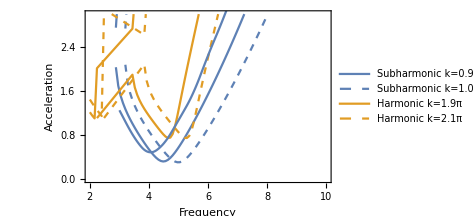

```mathematica
Show[p,ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],InterpolationOrder->2]]
```

#### subharmonic2

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs2/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.ssubs2/.ωd->freq0];
ord1=OrderingBy[evalsbase,Abs[Im[#]]&][[1;;2]];
ord2=OrderingBy[evalsbase2,Abs[Im[#]]&][[1;;2]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{300.369-6.93744×10^-9 ⅈ,300.369+6.94804×10^-9 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{184.681,Null}

{23.6423,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
v=rev[[All,ind1]];
w=lev[[All,ind2]];
Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,das,asmax,das}]
```

{20.6401,Null}{3.11516,Null}

1 300.369-6.93836×10^-9 ⅈ 6.59715 0.466117

2 300.214+3.91576×10^-8 ⅈ 0.000389703 0.000131376

3 300.214+3.9158×10^-8 ⅈ 4.23083×10^-13 1.62675×10^-13

4 300.214+3.91581×10^-8 ⅈ 1.90795×10^-14 2.15642×10^-15

5 300.214+3.9158×10^-8 ⅈ 3.30879×10^-14 3.39242×10^-15

6 300.214+3.91579×10^-8 ⅈ 1.77393×10^-14 3.43264×10^-15

7 300.214+3.9158×10^-8 ⅈ 3.05776×10^-14 4.45435×10^-15

8 300.214+3.91579×10^-8 ⅈ 2.82589×10^-14 4.08012×10^-15

9 300.214+3.91581×10^-8 ⅈ 2.732×10^-14 2.06047×10^-15

10 300.214+3.91579×10^-8 ⅈ 2.31206×10^-14 2.5933×10^-15

{19.3087,Null}{2.88016,Null}

1 299.916+1.30564×10^-7 ⅈ 6.39628 0.464572

2 299.813+1.74434×10^-7 ⅈ 0.000238944 0.0000833689

3 299.813+1.74434×10^-7 ⅈ 1.0541×10^-13 3.6734×10^-14

4 299.813+1.74434×10^-7 ⅈ 4.41957×10^-14 3.82059×10^-15

5 299.813+1.74434×10^-7 ⅈ 4.79945×10^-14 3.62153×10^-15

6 299.813+1.74434×10^-7 ⅈ 4.47677×10^-14 2.30265×10^-15

7 299.813+1.74435×10^-7 ⅈ 3.52635×10^-14 5.60608×10^-15

8 299.813+1.74434×10^-7 ⅈ 3.513×10^-14 3.69991×10^-15

9 299.813+1.74434×10^-7 ⅈ 5.48619×10^-14 3.98917×10^-15

10 299.813+1.74435×10^-7 ⅈ 3.69355×10^-14 5.40626×10^-15

{19.4837,Null}{2.8573,Null}

1 299.338+3.51133×10^-7 ⅈ 6.06169 0.460459

2 299.332+3.90834×10^-7 ⅈ 0.0000122135 4.46085×10^-6

3 299.332+3.90834×10^-7 ⅈ 2.88517×10^-14 2.46535×10^-15

4 299.332+3.90833×10^-7 ⅈ 2.84898×10^-14 3.19265×10^-15

5 299.332+3.90834×10^-7 ⅈ 2.89294×10^-14 3.40438×10^-15

6 299.332+3.90834×10^-7 ⅈ 2.47745×10^-14 3.20489×10^-15

7 299.332+3.90834×10^-7 ⅈ 2.53595×10^-14 3.53309×10^-15

8 299.332+3.90834×10^-7 ⅈ 2.31197×10^-14 3.09319×10^-15

9 299.332+3.90833×10^-7 ⅈ 2.68047×10^-14 3.34676×10^-15

10 299.332+3.90834×10^-7 ⅈ 2.96409×10^-14 2.73921×10^-15

{19.8363,Null}{2.88132,Null}

1 298.885+6.43036×10^-7 ⅈ 5.62224 0.454753

2 298.998+6.7669×10^-7 ⅈ 0.000193704 0.0000749082

3 298.998+6.7669×10^-7 ⅈ 5.30661×10^-14 1.68903×10^-14

4 298.998+6.7669×10^-7 ⅈ 3.96178×10^-14 4.13437×10^-15

5 298.998+6.7669×10^-7 ⅈ 2.87933×10^-14 2.94135×10^-15

6 298.998+6.7669×10^-7 ⅈ 3.84183×10^-14 3.39322×10^-15

7 298.998+6.7669×10^-7 ⅈ 3.54914×10^-14 3.34746×10^-15

8 298.998+6.7669×10^-7 ⅈ 3.12079×10^-14 2.50978×10^-15

9 298.998+6.7669×10^-7 ⅈ 3.02134×10^-14 4.15289×10^-15

10 298.998+6.7669×10^-7 ⅈ 3.15184×10^-14 3.86632×10^-15

{24.3131,Null}{2.8745,Null}

1 298.82+9.91557×10^-7 ⅈ 5.10839 0.4486

2 299.058+1.01657×10^-6 ⅈ 0.00033965 0.000140807

3 299.058+1.01657×10^-6 ⅈ 2.09379×10^-13 7.60283×10^-14

4 299.058+1.01657×10^-6 ⅈ 5.49724×10^-14 3.11545×10^-15

5 299.058+1.01657×10^-6 ⅈ 5.09274×10^-14 3.67065×10^-15

6 299.058+1.01657×10^-6 ⅈ 4.90057×10^-14 3.03789×10^-15

7 299.058+1.01657×10^-6 ⅈ 5.12324×10^-14 3.6691×10^-15

8 299.058+1.01657×10^-6 ⅈ 5.42725×10^-14 2.8767×10^-15

9 299.058+1.01657×10^-6 ⅈ 5.20576×10^-14 3.84671×10^-15

10 299.058+1.01657×10^-6 ⅈ 4.11088×10^-14 3.54698×10^-15

{20.0358,Null}{2.85315,Null}

1 299.402+1.37636×10^-6 ⅈ 4.5531 0.443032

2 299.776+1.3887×10^-6 ⅈ 0.000435194 0.00019619

3 299.776+1.3887×10^-6 ⅈ 3.22901×10^-13 1.32031×10^-13

4 299.776+1.3887×10^-6 ⅈ 6.0941×10^-14 4.82041×10^-15

5 299.776+1.3887×10^-6 ⅈ 5.73558×10^-14 3.91082×10^-15

6 299.776+1.3887×10^-6 ⅈ 4.846×10^-14 3.19882×10^-15

7 299.776+1.3887×10^-6 ⅈ 5.29566×10^-14 3.84015×10^-15

8 299.776+1.3887×10^-6 ⅈ 5.58638×10^-14 4.62029×10^-15

9 299.776+1.3887×10^-6 ⅈ 5.71995×10^-14 5.56036×10^-15

10 299.776+1.3887×10^-6 ⅈ 4.97939×10^-14 4.12645×10^-15

{20.9665,Null}{2.82019,Null}

1 300.92+1.76532×10^-6 ⅈ 3.98945 0.438916

2 301.456+1.75621×10^-6 ⅈ 0.000506231 0.00025235

3 301.456+1.75621×10^-6 ⅈ 3.7138×10^-13 1.68154×10^-13

4 301.456+1.75621×10^-6 ⅈ 6.03912×10^-14 5.13893×10^-15

5 301.456+1.75621×10^-6 ⅈ 6.19483×10^-14 5.01549×10^-15

6 301.456+1.75621×10^-6 ⅈ 5.3×10^-14 6.17129×10^-15

7 301.456+1.75621×10^-6 ⅈ 5.93999×10^-14 4.54028×10^-15

8 301.456+1.75621×10^-6 ⅈ 6.32655×10^-14 4.90234×10^-15

9 301.456+1.75621×10^-6 ⅈ 5.89355×10^-14 4.72097×10^-15

10 301.456+1.75621×10^-6 ⅈ 6.19189×10^-14 4.76045×10^-15

{21.051,Null}{2.98802,Null}

1 303.742+2.0935×10^-6 ⅈ 3.44616 0.43709

2 304.494+2.0354×10^-6 ⅈ 0.000575375 0.000323416

3 304.494+2.03541×10^-6 ⅈ 3.57194×10^-13 1.82269×10^-13

4 304.494+2.03541×10^-6 ⅈ 7.67157×10^-14 6.42141×10^-15

5 304.494+2.03541×10^-6 ⅈ 7.28438×10^-14 7.3038×10^-15

6 304.494+2.03541×10^-6 ⅈ 7.44273×10^-14 8.99077×10^-15

7 304.494+2.03541×10^-6 ⅈ 7.97958×10^-14 7.91458×10^-15

8 304.494+2.03541×10^-6 ⅈ 7.42885×10^-14 9.18029×10^-15

9 304.494+2.03541×10^-6 ⅈ 7.63294×10^-14 7.94485×10^-15

10 304.494+2.03541×10^-6 ⅈ 7.56892×10^-14 1.12135×10^-14

{21.9934,Null}{3.05624,Null}

1 308.386+2.18895×10^-6 ⅈ 2.94451 0.43864

2 309.446+1.98933×10^-6 ⅈ 0.000657773 0.000426511

3 309.446+1.98935×10^-6 ⅈ 2.43774×10^-13 1.37126×10^-13

4 309.446+1.98935×10^-6 ⅈ 9.53544×10^-14 7.29252×10^-15

5 309.446+1.98935×10^-6 ⅈ 8.8769×10^-14 7.81635×10^-15

6 309.446+1.98935×10^-6 ⅈ 8.51801×10^-14 8.42082×10^-15

7 309.446+1.98935×10^-6 ⅈ 8.19061×10^-14 8.65286×10^-15

8 309.446+1.98935×10^-6 ⅈ 1.04535×10^-13 7.19322×10^-15

9 309.446+1.98935×10^-6 ⅈ 8.98101×10^-14 1.09756×10^-14

10 309.446+1.98935×10^-6 ⅈ 7.83737×10^-14 8.44445×10^-15

{22.1834,Null}{3.19575,Null}

1 315.611+1.53324×10^-6 ⅈ 2.49748 0.445346

2 317.124+9.04323×10^-7 ⅈ 0.000764462 0.000586999

3 317.124+9.04369×10^-7 ⅈ 2.38299×10^-13 1.77131×10^-13

4 317.124+9.04369×10^-7 ⅈ 1.10181×10^-13 1.21437×10^-14

5 317.124+9.04369×10^-7 ⅈ 1.0567×10^-13 1.09025×10^-14

6 317.124+9.04369×10^-7 ⅈ 1.15417×10^-13 1.61518×10^-14

7 317.124+9.04369×10^-7 ⅈ 1.04961×10^-13 1.03273×10^-14

8 317.124+9.04369×10^-7 ⅈ 1.10115×10^-13 9.99197×10^-15

9 317.124+9.04369×10^-7 ⅈ 1.1972×10^-13 1.02191×10^-14

10 317.124+9.04369×10^-7 ⅈ 1.14438×10^-13 1.2673×10^-14

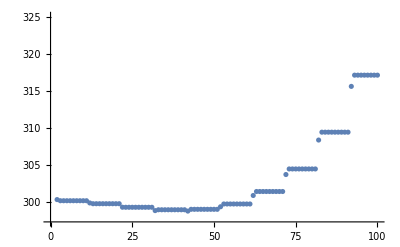

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λps2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λps2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{22.384,Null}{3.03108,Null}

1 317.124+9.04369×10^-7 ⅈ 1.14463×10^-13 1.22513×10^-14

2 317.124+9.04369×10^-7 ⅈ 1.02009×10^-13 9.80525×10^-15

3 317.124+9.04369×10^-7 ⅈ 1.13067×10^-13 9.50563×10^-15

4 317.124+9.04369×10^-7 ⅈ 9.92099×10^-14 1.34153×10^-14

5 317.124+9.04369×10^-7 ⅈ 1.08332×10^-13 1.06751×10^-14

6 317.124+9.04369×10^-7 ⅈ 1.05422×10^-13 1.10743×10^-14

7 317.124+9.04369×10^-7 ⅈ 1.06683×10^-13 1.39891×10^-14

8 317.124+9.04369×10^-7 ⅈ 1.13589×10^-13 1.00764×10^-14

9 317.124+9.04369×10^-7 ⅈ 1.09895×10^-13 1.23233×10^-14

10 317.124+9.04369×10^-7 ⅈ 1.04375×10^-13 1.90038×10^-14

{22.8895,Null}{3.09183,Null}

1 341.284-0.0000423857 ⅈ 3.3657 3.08608

2 525.385-0.000257771 ⅈ 0.594391 1.14588

3 537.134-0.000163421 ⅈ 0.00617096 0.01276

4 537.135-0.000163039 ⅈ 9.99025×10^-9 1.80103×10^-8

5 537.135-0.000163039 ⅈ 1.9785×10^-13 2.88305×10^-14

6 537.135-0.000163039 ⅈ 1.98989×10^-13 3.08386×10^-14

7 537.135-0.000163039 ⅈ 2.02744×10^-13 2.73298×10^-14

8 537.135-0.000163039 ⅈ 2.00352×10^-13 3.29257×10^-14

9 537.135-0.000163039 ⅈ 1.92313×10^-13 2.80273×10^-14

10 537.135-0.000163039 ⅈ 2.19376×10^-13 2.74896×10^-14

{21.625,Null}{2.991,Null}

1 895.456+0.00180802 ⅈ 3.08317 4.80807

2 927.551-0.00180959 ⅈ 0.0501117 0.0514732

3 927.55-0.00183046 ⅈ 2.48272×10^-8 1.9297×10^-8

4 927.55-0.00183046 ⅈ 3.69207×10^-13 7.78336×10^-14

5 927.55-0.00183046 ⅈ 3.50717×10^-13 8.23543×10^-14

6 927.55-0.00183046 ⅈ 3.82426×10^-13 7.81466×10^-14

7 927.55-0.00183046 ⅈ 3.52873×10^-13 7.48811×10^-14

8 927.55-0.00183046 ⅈ 4.16225×10^-13 8.07292×10^-14

9 927.55-0.00183046 ⅈ 3.66142×10^-13 7.47166×10^-14

10 927.55-0.00183046 ⅈ 3.68849×10^-13 7.85117×10^-14

{22.7118,Null}{3.16748,Null}

1 1358.51-0.00952828 ⅈ 3.01624 10.566

2 1389.55-0.0333098 ⅈ 0.126141 0.0709528

3 1389.39-0.109776 ⅈ 0.00061008 0.000255174

4 1389.39-0.109802 ⅈ 7.44614×10^-10 3.22481×10^-10

5 1389.39-0.109802 ⅈ 1.20506×10^-12 1.06477×10^-12

6 1389.39-0.109802 ⅈ 1.11766×10^-12 1.06462×10^-12

7 1389.39-0.109802 ⅈ 1.10056×10^-12 1.06096×10^-12

8 1389.39-0.109802 ⅈ 1.18667×10^-12 9.27174×10^-13

9 1389.39-0.109802 ⅈ 1.10084×10^-12 9.72418×10^-13

10 1389.39-0.109802 ⅈ 1.17652×10^-12 9.74663×10^-13

{21.7716,Null}{2.97117,Null}

1 1826.15-8.47988 ⅈ 4.35481 140.501

2 1877.3-0.15827 ⅈ 0.335241 0.140922

3 1877.52-0.0185708 ⅈ 0.000135259 0.0000596237

4 1877.52-0.0185708 ⅈ 1.19976×10^-12 5.28976×10^-13

5 1877.52-0.0185708 ⅈ 1.22048×10^-12 4.19834×10^-13

6 1877.52-0.0185708 ⅈ 1.31403×10^-12 4.41129×10^-13

7 1877.52-0.0185708 ⅈ 1.25774×10^-12 4.43234×10^-13

8 1877.52-0.0185708 ⅈ 1.34901×10^-12 4.61292×10^-13

9 1877.52-0.0185708 ⅈ 1.33901×10^-12 4.01205×10^-13

10 1877.52-0.0185708 ⅈ 1.30807×10^-12 4.75496×10^-13

{21.2813,Null}{2.96013,Null}

1 2399.77-0.0467573 ⅈ 3.3835 52.2125

2 2403.53+0.233155 ⅈ 0.0182846 0.00583148

3 2403.53+0.243471 ⅈ 8.25398×10^-6 2.64333×10^-6

4 2403.53+0.243471 ⅈ 5.12756×10^-12 4.00816×10^-12

5 2403.53+0.243471 ⅈ 5.95423×10^-12 4.61003×10^-12

6 2403.53+0.243471 ⅈ 5.24463×10^-12 4.02738×10^-12

7 2403.53+0.243471 ⅈ 5.80289×10^-12 4.22642×10^-12

8 2403.53+0.243471 ⅈ 5.12402×10^-12 4.13423×10^-12

9 2403.53+0.243471 ⅈ 5.47019×10^-12 5.10994×10^-12

10 2403.53+0.243471 ⅈ 5.60569×10^-12 4.4715×10^-12

{22.2427,Null}{2.86755,Null}

1 2978.84+16.8374 ⅈ 4.87458 333.124

2 2962.89-0.198217 ⅈ 0.134369 0.0414075

3 2962.91-0.207773 ⅈ 7.02517×10^-6 3.20055×10^-6

4 2962.91-0.207773 ⅈ 6.36573×10^-12 6.10289×10^-12

5 2962.91-0.207773 ⅈ 6.18214×10^-12 6.89953×10^-12

6 2962.91-0.207773 ⅈ 6.07421×10^-12 6.67916×10^-12

7 2962.91-0.207773 ⅈ 5.90661×10^-12 7.11614×10^-12

8 2962.91-0.207773 ⅈ 5.87677×10^-12 7.52249×10^-12

9 2962.91-0.207773 ⅈ 6.18767×10^-12 6.9366×10^-12

10 2962.91-0.207773 ⅈ 6.15067×10^-12 7.73793×10^-12

{26.9731,Null}{3.26884,Null}

1 3552.69-1.72943 ⅈ 4.12589 806.19

2 3521.3+3.37341 ⅈ 0.328024 0.100276

3 3517.95+6.66871 ⅈ 0.0246415 0.0100093

4 3517.98+6.67442 ⅈ 0.0000181845 7.41188×10^-6

5 3517.98+6.67442 ⅈ 4.24267×10^-11 1.04066×10^-11

6 3517.98+6.67442 ⅈ 5.09363×10^-11 8.91256×10^-12

7 3517.98+6.67442 ⅈ 4.89521×10^-11 9.904×10^-12

8 3517.98+6.67442 ⅈ 3.841×10^-11 1.01462×10^-11

9 3517.98+6.67442 ⅈ 4.8164×10^-11 1.02539×10^-11

10 3517.98+6.67442 ⅈ 3.68725×10^-11 9.24345×10^-12

{22.248,Null}{2.87625,Null}

1 2779.36+979.921 ⅈ 19.3307 1929.24

2 4958.35-273.667 ⅈ 37.0512 7.62966

3 4858.63-148.621 ⅈ 3.34811 4.22944

4 5052.4-20.4634 ⅈ 0.936835 3.21543

5 5026.59-6.6325 ⅈ 0.0450193 0.144512

6 5026.59-6.60337 ⅈ 3.98732×10^-6 5.15314×10^-6

7 5026.59-6.60337 ⅈ 1.01508×10^-10 9.00087×10^-11

8 5026.59-6.60337 ⅈ 9.83194×10^-11 9.92468×10^-11

9 5026.59-6.60337 ⅈ 9.23772×10^-11 9.38206×10^-11

10 5026.59-6.60337 ⅈ 9.22235×10^-11 9.90918×10^-11

{22.7042,Null}{2.88992,Null}

1 6323.05-12.397 ⅈ 20.1776 10968.2

2 6219.75-1.7008 ⅈ 0.621889 0.276504

3 6219.38+4.96624 ⅈ 0.0330812 0.0169036

4 6219.36+4.96405 ⅈ 5.05687×10^-6 2.70292×10^-6

5 6219.36+4.96405 ⅈ 1.98361×10^-10 3.75945×10^-10

6 6219.36+4.96405 ⅈ 1.82739×10^-10 3.6675×10^-10

7 6219.36+4.96405 ⅈ 1.88541×10^-10 4.60795×10^-10

8 6219.36+4.96405 ⅈ 1.83538×10^-10 3.81423×10^-10

9 6219.36+4.96405 ⅈ 1.72119×10^-10 3.55202×10^-10

10 6219.36+4.96405 ⅈ 1.95971×10^-10 3.60048×10^-10

{22.1824,Null}{3.03199,Null}

1 7372.52+129.851 ⅈ 29.7507 30141.7

2 7460.18+34.7776 ⅈ 1.38199 0.58096

3 7470.8+24.711 ⅈ 0.0661993 0.0293893

4 7470.84+24.6767 ⅈ 0.0000154964 6.99871×10^-6

5 7470.84+24.6767 ⅈ 4.41169×10^-10 4.46001×10^-10

6 7470.84+24.6767 ⅈ 3.83454×10^-10 4.70637×10^-10

7 7470.84+24.6767 ⅈ 3.91844×10^-10 4.78103×10^-10

8 7470.84+24.6767 ⅈ 4.17322×10^-10 4.61366×10^-10

9 7470.84+24.6767 ⅈ 3.90653×10^-10 4.14533×10^-10

10 7470.84+24.6767 ⅈ 3.99755×10^-10 4.17908×10^-10

{586.118,Null}

```mathematica
w=w0;
v=v0;
λms2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λms2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{21.7079,Null}{2.9606,Null}

1 317.124+9.04369×10^-7 ⅈ 1.14463×10^-13 1.22513×10^-14

2 317.124+9.04369×10^-7 ⅈ 1.02009×10^-13 9.80525×10^-15

3 317.124+9.04369×10^-7 ⅈ 1.13067×10^-13 9.50563×10^-15

4 317.124+9.04369×10^-7 ⅈ 9.92099×10^-14 1.34153×10^-14

5 317.124+9.04369×10^-7 ⅈ 1.08332×10^-13 1.06751×10^-14

6 317.124+9.04369×10^-7 ⅈ 1.05422×10^-13 1.10743×10^-14

7 317.124+9.04369×10^-7 ⅈ 1.06683×10^-13 1.39891×10^-14

8 317.124+9.04369×10^-7 ⅈ 1.13589×10^-13 1.00764×10^-14

9 317.124+9.04369×10^-7 ⅈ 1.09895×10^-13 1.23233×10^-14

10 317.124+9.04369×10^-7 ⅈ 1.04375×10^-13 1.90038×10^-14

{21.488,Null}{3.0549,Null}

1 293.99+0.0000409108 ⅈ 3.39912 3.36069

2 474.298-0.0000289686 ⅈ 0.638492 1.41122

3 487.041-0.000075204 ⅈ 0.010728 0.025909

4 487.028-0.0000743665 ⅈ 7.62987×10^-7 1.46506×10^-6

5 487.028-0.0000743665 ⅈ 1.01329×10^-13 2.433×10^-14

6 487.028-0.0000743665 ⅈ 1.08941×10^-13 1.69565×10^-14

7 487.028-0.0000743665 ⅈ 1.02036×10^-13 1.66917×10^-14

8 487.028-0.0000743665 ⅈ 9.68734×10^-14 1.78532×10^-14

9 487.028-0.0000743665 ⅈ 1.07421×10^-13 1.66346×10^-14

10 487.028-0.0000743665 ⅈ 9.74368×10^-14 1.53234×10^-14

{21.0939,Null}{3.07699,Null}

1 732.733-0.000453263 ⅈ 2.64127 4.37584

2 842.381-0.0022303 ⅈ 0.295909 0.839588

3 853.525-0.00332773 ⅈ 0.00905045 0.0252638

4 853.536-0.00333084 ⅈ 2.5231×10^-7 7.02147×10^-7

5 853.536-0.00333084 ⅈ 1.21779×10^-13 3.50309×10^-14

6 853.536-0.00333084 ⅈ 1.0885×10^-13 3.6356×10^-14

7 853.536-0.00333084 ⅈ 1.13454×10^-13 3.33247×10^-14

8 853.536-0.00333084 ⅈ 1.18259×10^-13 4.52336×10^-14

9 853.536-0.00333084 ⅈ 1.10685×10^-13 3.26345×10^-14

10 853.536-0.00333084 ⅈ 1.13634×10^-13 4.34014×10^-14

{21.542,Null}{2.93476,Null}

1 1221.67-0.00931317 ⅈ 2.36788 6.75355

2 1321.79-0.141805 ⅈ 0.0515941 0.258126

3 1321.87-0.175202 ⅈ 7.5568×10^-6 0.0000773164

4 1321.87-0.175202 ⅈ 1.62955×10^-13 7.97785×10^-14

5 1321.87-0.175202 ⅈ 1.49753×10^-13 7.62439×10^-14

6 1321.87-0.175202 ⅈ 1.51313×10^-13 8.16074×10^-14

7 1321.87-0.175202 ⅈ 1.47455×10^-13 7.91522×10^-14

8 1321.87-0.175202 ⅈ 1.45358×10^-13 7.31753×10^-14

9 1321.87-0.175202 ⅈ 1.66817×10^-13 7.27231×10^-14

10 1321.87-0.175202 ⅈ 1.56532×10^-13 7.53765×10^-14

{21.0819,Null}{2.83371,Null}

1 1898.06-1.18125 ⅈ 3.20775 12.4179

2 1553.65-19.8423 ⅈ 4.15349 8.7984

3 1603.23+80.957 ⅈ 14.2127 13.3907

4 1623.29+1.44153 ⅈ 2.84943 4.77524

5 1609.87-34.5287 ⅈ 2.48981 2.97224

6 1595.65-29.663 ⅈ 0.473115 0.344668

7 1595.83-29.77 ⅈ 0.00220447 0.0077989

8 1595.83-29.7672 ⅈ 0.0000204627 0.0000803807

9 1595.83-29.7672 ⅈ 2.0983×10^-11 8.22375×10^-11

10 1595.83-29.7672 ⅈ 1.15308×10^-12 6.0032×10^-13

{21.1637,Null}{2.90595,Null}

1 1751.21-10.353 ⅈ 14.7995 34.9065

2 1755.03-11.2848 ⅈ 0.0352407 0.0893928

3 1755.04-11.2857 ⅈ 0.0000429236 0.0000801351

4 1755.04-11.2857 ⅈ 4.10143×10^-11 7.65356×10^-11

5 1755.04-11.2857 ⅈ 6.26643×10^-13 3.17247×10^-13

6 1755.04-11.2857 ⅈ 5.50119×10^-13 3.15188×10^-13

7 1755.04-11.2857 ⅈ 5.30289×10^-13 3.16946×10^-13

8 1755.04-11.2857 ⅈ 5.86256×10^-13 2.93904×10^-13

9 1755.04-11.2857 ⅈ 5.59348×10^-13 3.3524×10^-13

10 1755.04-11.2857 ⅈ 5.77874×10^-13 3.087×10^-13

{20.8628,Null}{2.96937,Null}

1 1900.99+4.34794 ⅈ 11.6764 28.7985

2 1924.95+5.91667 ⅈ 0.389588 0.97084

3 1926.13+6.75998 ⅈ 0.0177311 0.0358046

4 1926.13+6.75879 ⅈ 7.04799×10^-6 0.0000116829

5 1926.13+6.75879 ⅈ 2.88049×10^-13 2.91212×10^-13

6 1926.13+6.75879 ⅈ 3.03747×10^-13 2.54195×10^-13

7 1926.13+6.75879 ⅈ 3.03616×10^-13 2.27282×10^-13

8 1926.13+6.75879 ⅈ 3.30497×10^-13 2.61616×10^-13

9 1926.13+6.75879 ⅈ 2.92241×10^-13 2.82897×10^-13

10 1926.13+6.75879 ⅈ 3.142×10^-13 3.12812×10^-13

{361.461,Null}

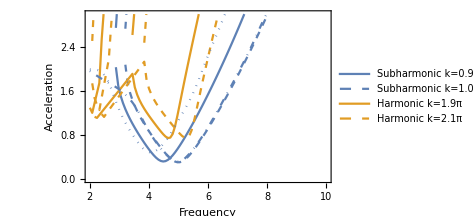

```mathematica
Show[p,ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],DotDashed],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dotted],InterpolationOrder->2]]
```

#### harmonic

```mathematica
hsubs1={g->980,σ->20,qx->0,qy->2*Pi/2*0.95,μ->0.005,ρ->1,h0->0.1,ω->0*ωd};
hsubs1={g->980,σ->20,qx->0,qy->2*Pi/2*0.95,μ->0.005,ρ->1,h0->0.1,ω->0*ωd};
hsubs1={g->980,σ->20,qx->0,qy->2*Pi/2*0.95,μ->0.005,ρ->1,h0->0.1,ω->ωd};
hsubs1={g->980,σ->20,qx->0,qy->2*Pi/2*0.95,μ->0.005,ρ->1,h0->0.1,ω->0.000001*ωd};
```

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.hsubs1/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Transpose[eq1base],Transpose[eq2base]}/.subs/.hsubs1/.ωd->freq0];
ord1=OrderingBy[evalsbase,Abs[#]&][[1;;4]];
ord2=OrderingBy[evalsbase2,Abs[#]&][[1;;4]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{1231.58+0.00458355 ⅈ,1231.58+0.00458355 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.hsubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.hsubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{182.047,Null}

{24.865,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
v=rev[[All,ind1]];
w=lev[[All,ind2]];
AbsoluteTiming[Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[
λ=w.test1.v/(w.test2.v);
v=LinearSolve[(λ*test2-test1),test2.v,Method->"Multifrontal"];
w=LinearSolve[Transpose[(λ*test2-test1)],Transpose[test2].w,Method->"Multifrontal"];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Transpose[test1-λ*test2].w]];
AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
,{k,1,10}]]
,{As,das,asmax,das}]]
```

{18.4621,Null}{2.85856,Null}

1 1231.58+0.00458355 ⅈ 0.0000791193 0.217367

2 1247.29-0.00551417 ⅈ 1.90732×10^-7 0.000615982

3 1247.33-0.00557103 ⅈ 2.39292×10^-15 8.37725×10^-12

4 1247.33-0.00557103 ⅈ 5.11281×10^-16 1.65514×10^-12

5 1247.33-0.00557103 ⅈ 7.61594×10^-16 2.46768×10^-12

6 1247.33-0.00557103 ⅈ 9.68195×10^-16 2.28835×10^-12

7 1247.33-0.00557103 ⅈ 7.99446×10^-16 1.81614×10^-12

8 1247.33-0.00557103 ⅈ 7.49544×10^-16 1.50514×10^-12

9 1247.33-0.00557103 ⅈ 5.86076×10^-16 1.88847×10^-12

10 1247.33-0.00557103 ⅈ 3.44606×10^-16 1.9581×10^-12

{19.049,Null}{2.86924,Null}

1 1284.94+0.0032081 ⅈ 0.000026355 0.217868

2 1299.73+0.000748632 ⅈ 1.72623×10^-8 0.000219001

3 1299.75+0.000743023 ⅈ 5.8979×10^-16 4.38446×10^-12

4 1299.75+0.000743023 ⅈ 5.21936×10^-16 5.8602×10^-12

5 1299.75+0.000743023 ⅈ 4.04322×10^-16 6.82725×10^-12

6 1299.75+0.000743023 ⅈ 4.31363×10^-16 4.44755×10^-12

7 1299.75+0.000743023 ⅈ 4.45532×10^-16 6.5384×10^-12

8 1299.75+0.000743023 ⅈ 6.99×10^-16 2.48358×10^-12

9 1299.75+0.000743023 ⅈ 5.73929×10^-16 3.57741×10^-12

10 1299.75+0.000743023 ⅈ 4.37447×10^-16 2.91302×10^-12

{19.293,Null}{2.85715,Null}

1 1364.42+0.00681556 ⅈ 3.21742×10^-6 0.0749634

2 1368.8+0.0119189 ⅈ 4.94939×10^-10 0.0000175409

3 1368.79+0.0119182 ⅈ 3.82465×10^-16 1.86528×10^-11

4 1368.79+0.0119182 ⅈ 5.41827×10^-16 3.12022×10^-12

5 1368.79+0.0119182 ⅈ 6.86738×10^-16 1.14716×10^-11

6 1368.79+0.0119182 ⅈ 5.52107×10^-16 1.35187×10^-11

7 1368.79+0.0119182 ⅈ 4.49107×10^-16 1.73248×10^-11

8 1368.79+0.0119182 ⅈ 6.67386×10^-16 1.7731×10^-11

9 1368.79+0.0119182 ⅈ 5.89037×10^-16 9.19443×10^-12

10 1368.79+0.0119182 ⅈ 6.97691×10^-16 1.62094×10^-11

{19.6902,Null}{2.86895,Null}

1 1435.96+0.0312536 ⅈ 0.0000111331 0.631096

2 1402.36+0.0608038 ⅈ 2.63903×10^-7 0.0140663

3 1401.9+0.0618984 ⅈ 1.0058×10^-12 5.47873×10^-8

4 1401.9+0.0618985 ⅈ 2.14496×10^-15 2.13054×10^-11

5 1401.9+0.0618985 ⅈ 3.92267×10^-15 5.04764×10^-11

6 1401.9+0.0618985 ⅈ 1.67191×10^-15 2.29889×10^-11

7 1401.9+0.0618985 ⅈ 2.08904×10^-15 8.30217×10^-12

8 1401.9+0.0618985 ⅈ 1.35285×10^-15 4.00423×10^-11

9 1401.9+0.0618985 ⅈ 1.39105×10^-15 3.02737×10^-11

10 1401.9+0.0618985 ⅈ 2.44558×10^-15 1.23362×10^-11

$Aborted

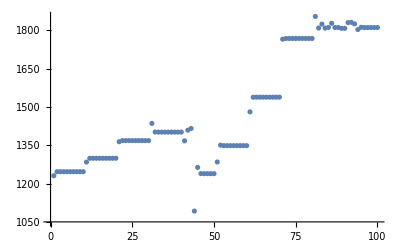

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λph1={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ 
λ=w.test1.v/(w.test2.v);
v=LinearSolve[(λ*test2-test1),test2.v,Method->"Multifrontal"];
w=LinearSolve[Transpose[(λ*test2-test1)],Transpose[test2].w,Method->"Multifrontal"];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Transpose[test1-λ*test2].w]];
AppendTo[λph1,λ];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq/2}]]
```

{20.2002,Null}{2.81414,Null}

1 1810.66+0.000865973 ⅈ 7.57321×10^-16 2.95648×10^-10

2 1810.66+0.000865973 ⅈ 1.37135×10^-15 6.25573×10^-11

3 1810.66+0.000865973 ⅈ 8.66715×10^-16 2.25533×10^-10

4 1810.66+0.000865973 ⅈ 8.21897×10^-16 1.56467×10^-10

5 1810.66+0.000865973 ⅈ 9.20185×10^-16 3.63944×10^-10

6 1810.66+0.000865973 ⅈ 1.14416×10^-15 4.38464×10^-10

7 1810.66+0.000865973 ⅈ 8.59363×10^-16 4.87639×10^-10

8 1810.66+0.000865973 ⅈ 8.15433×10^-16 1.3193×10^-10

9 1810.66+0.000865973 ⅈ 8.28974×10^-16 3.06006×10^-10

10 1810.66+0.000865973 ⅈ 1.07336×10^-15 1.93671×10^-10

{20.4874,Null}{2.84538,Null}

1 1646.63-0.0203808 ⅈ 8.83215×10^-6 2.08667

2 1695.33+0.076625 ⅈ 0.0000201393 1.47887

3 1673.16+0.0436836 ⅈ 2.72714×10^-6 1.87711

4 1677.71+0.189667 ⅈ 7.08255×10^-6 0.217701

5 1766.03+29.5893 ⅈ 0.0000546363 4.81388

6 1701.39+10.2817 ⅈ 0.0000217607 1.69372

7 1676.91+5.03572 ⅈ 3.83629×10^-6 1.05428

8 1672.07+16.3533 ⅈ 1.50942×10^-6 0.156938

9 1671.14+12.6225 ⅈ 2.638×10^-8 0.00296199

10 1671.1+12.5737 ⅈ 1.59544×10^-13 1.85182×10^-8

{20.4685,Null}{2.84845,Null}

1 1519.83-0.211598 ⅈ 0.000011785 1.13404

2 1503.72-5.74636 ⅈ 3.80444×10^-6 0.234879

3 1505.61+0.00855854 ⅈ 1.75884×10^-8 0.00118886

4 1505.58-0.00102639 ⅈ 1.61963×10^-15 1.07875×10^-10

5 1505.58-0.00102639 ⅈ 7.96954×10^-16 3.25687×10^-11

6 1505.58-0.00102639 ⅈ 8.00586×10^-16 5.31325×10^-11

7 1505.58-0.00102639 ⅈ 1.24903×10^-15 5.19035×10^-11

8 1505.58-0.00102639 ⅈ 1.38373×10^-15 3.00406×10^-11

9 1505.58-0.00102639 ⅈ 1.31649×10^-15 6.11594×10^-11

10 1505.58-0.00102639 ⅈ 1.04775×10^-15 2.93805×10^-11

{20.7409,Null}{2.88205,Null}

1 1350.72+0.0100807 ⅈ 0.0000492728 6.02012

2 1749.08+0.0502095 ⅈ 0.0000507385 17.0679

3 1496.31+0.0215696 ⅈ 4.54137×10^-6 0.387332

4 1498.61+0.0189858 ⅈ 1.20219×10^-6 0.0840304

5 1500.61+0.00324147 ⅈ 1.31199×10^-8 0.000833539

6 1500.63+0.00286822 ⅈ 1.12042×10^-14 6.994×10^-10

7 1500.63+0.00286822 ⅈ 6.08503×10^-16 3.78312×10^-11

8 1500.63+0.00286822 ⅈ 8.38011×10^-16 2.06713×10^-11

9 1500.63+0.00286822 ⅈ 9.01749×10^-16 2.64146×10^-11

10 1500.63+0.00286822 ⅈ 9.59435×10^-16 1.59231×10^-11

{20.425,Null}{2.83164,Null}

1 1299.2+0.0209584 ⅈ 0.0000647377 4.37541

2 1693.84+0.177732 ⅈ 0.0000336261 15.0217

3 1490.66-0.556426 ⅈ 0.000010431 2.2582

4 1705.83+0.943153 ⅈ 0.0000177913 3.21963

5 1634.04-0.0365634 ⅈ 1.80137×10^-7 0.0385752

6 1635.67+0.0127101 ⅈ 6.34622×10^-12 1.22634×10^-6

7 1635.67+0.012716 ⅈ 1.00174×10^-15 6.28849×10^-11

8 1635.67+0.012716 ⅈ 9.01708×10^-16 1.59847×10^-11

9 1635.67+0.012716 ⅈ 1.16221×10^-15 7.73015×10^-11

10 1635.67+0.012716 ⅈ 8.9901×10^-16 4.68969×10^-11

{20.5264,Null}{2.84086,Null}

1 2493.72-0.211324 ⅈ 0.00021954 6.92867

2 2210.15+0.0242401 ⅈ 8.61886×10^-7 0.134761

3 2219.19+0.00648601 ⅈ 1.10861×10^-10 0.0000138317

4 2219.19+0.0064812 ⅈ 8.5897×10^-16 2.79708×10^-11

5 2219.19+0.0064812 ⅈ 1.06591×10^-15 2.82832×10^-11

6 2219.19+0.0064812 ⅈ 9.39112×10^-16 2.41412×10^-11

7 2219.19+0.0064812 ⅈ 1.05451×10^-15 2.29844×10^-11

8 2219.19+0.0064812 ⅈ 9.02135×10^-16 1.46351×10^-11

9 2219.19+0.0064812 ⅈ 1.06636×10^-15 2.19682×10^-11

10 2219.19+0.0064812 ⅈ 1.05148×10^-15 2.09667×10^-11

{21.0373,Null}{2.92876,Null}

1 2751.07-0.00574176 ⅈ 3.85511×10^-6 0.0739222

2 2756.62-0.00238753 ⅈ 5.90662×10^-7 0.0638537

3 2756.14-0.00393825 ⅈ 1.67907×10^-6 0.21014

4 2750.63-0.104541 ⅈ 2.23741×10^-6 0.537292

5 2755.11-0.0418119 ⅈ 5.9656×10^-7 0.120904

6 2757.78-0.0731486 ⅈ 2.00302×10^-6 0.15034

7 2749.66-7.98464 ⅈ 4.27567×10^-6 0.961106

8 2754.58-2.80133 ⅈ 9.41648×10^-7 0.225653

9 2756.42-1.37695 ⅈ 1.81033×10^-7 0.0299859

10 2756.87-1.50398 ⅈ 5.61375×10^-9 0.000862473

{20.4383,Null}{2.85096,Null}

1 3005.47-292.1 ⅈ 0.000111536 32.0106

2 3164.79+364.331 ⅈ 0.00019937 32.298

3 3183.5-64.1942 ⅈ 0.0000467256 7.34525

4 3289.03-9.46758 ⅈ 1.87411×10^-6 0.273809

5 3283.38+0.63717 ⅈ 2.09237×10^-7 0.0110581

6 3283.48-0.00264993 ⅈ 8.71255×10^-10 0.0000488336

7 3283.48-0.000626948 ⅈ 7.10465×10^-16 3.61304×10^-11

8 3283.48-0.000626948 ⅈ 8.22558×10^-16 3.27284×10^-11

9 3283.48-0.000626948 ⅈ 6.8372×10^-16 4.00224×10^-11

10 3283.48-0.000626948 ⅈ 6.52173×10^-16 4.5131×10^-11

{20.5697,Null}{2.8261,Null}

1 3793.24+0.0628991 ⅈ 2.05874×10^-6 0.352478

2 3793.34+0.0992288 ⅈ 8.05543×10^-7 0.20886

3 3796.19+0.0325659 ⅈ 9.07715×10^-9 0.00210564

4 3796.22+0.0308303 ⅈ 1.17848×10^-14 2.76506×10^-9

5 3796.22+0.0308303 ⅈ 8.59047×10^-16 1.18199×10^-10

6 3796.22+0.0308303 ⅈ 8.26349×10^-16 1.69401×10^-10

7 3796.22+0.0308303 ⅈ 8.64647×10^-16 1.42915×10^-10

8 3796.22+0.0308303 ⅈ 8.80231×10^-16 1.48089×10^-10

9 3796.22+0.0308303 ⅈ 8.79653×10^-16 1.92112×10^-10

10 3796.22+0.0308303 ⅈ 7.31507×10^-16 2.49808×10^-10

{20.8664,Null}{3.07615,Null}

1 3692.06-0.185874 ⅈ 0.000051283 5.19885

2 3737.73-0.20565 ⅈ 2.69695×10^-7 0.282774

3 3738.18-0.0744057 ⅈ 4.65009×10^-8 0.0156308

4 3738.26+0.0034417 ⅈ 1.30988×10^-12 4.75441×10^-7

5 3738.26+0.00344428 ⅈ 6.04285×10^-16 1.88208×10^-10

6 3738.26+0.00344428 ⅈ 4.12972×10^-16 2.34916×10^-10

7 3738.26+0.00344428 ⅈ 1.24353×10^-15 2.13671×10^-10

8 3738.26+0.00344428 ⅈ 7.26615×10^-16 2.08694×10^-10

9 3738.26+0.00344428 ⅈ 4.75504×10^-16 2.00171×10^-10

10 3738.26+0.00344428 ⅈ 7.18562×10^-16 1.93473×10^-10

{22.1528,Null}{2.9336,Null}

1 3695.05-0.0577815 ⅈ 8.42618×10^-6 1.54657

2 3686.51+0.0133823 ⅈ 2.37778×10^-7 0.179972

3 3687.52+0.000490685 ⅈ 1.14715×10^-10 0.0000778735

4 3687.52+0.000473303 ⅈ 4.98053×10^-16 3.15459×10^-10

5 3687.52+0.000473303 ⅈ 5.52882×10^-16 2.93672×10^-10

6 3687.52+0.000473303 ⅈ 5.43551×10^-16 2.96233×10^-10

7 3687.52+0.000473303 ⅈ 6.0512×10^-16 2.54769×10^-10

8 3687.52+0.000473303 ⅈ 4.30718×10^-16 2.19342×10^-10

9 3687.52+0.000473303 ⅈ 6.58941×10^-16 2.12804×10^-10

10 3687.52+0.000473303 ⅈ 3.40444×10^-16 2.43363×10^-10

{21.6879,Null}{2.91238,Null}

1 3625.26+0.00311949 ⅈ 2.50727×10^-6 2.28614

2 3610.75+0.00110365 ⅈ 7.38576×10^-9 0.00530196

3 3610.78+0.00117901 ⅈ 6.67872×10^-16 4.98645×10^-10

4 3610.78+0.00117901 ⅈ 5.70137×10^-16 4.02553×10^-10

5 3610.78+0.00117901 ⅈ 5.65876×10^-16 5.02794×10^-10

6 3610.78+0.00117901 ⅈ 6.96973×10^-16 4.2391×10^-10

7 3610.78+0.00117901 ⅈ 4.87988×10^-16 3.7374×10^-10

8 3610.78+0.00117901 ⅈ 6.18953×10^-16 4.26124×10^-10

9 3610.78+0.00117901 ⅈ 4.9671×10^-16 3.93534×10^-10

10 3610.78+0.00117901 ⅈ 6.07597×10^-16 3.78034×10^-10

{21.4226,Null}{3.02738,Null}

1 3537.59-0.00156675 ⅈ 1.48224×10^-6 1.0432

2 3530.57+0.0010552 ⅈ 3.07103×10^-10 0.000251515

3 3530.57+0.00105323 ⅈ 5.58697×10^-16 5.6612×10^-10

4 3530.57+0.00105323 ⅈ 6.01301×10^-16 5.63349×10^-10

5 3530.57+0.00105324 ⅈ 6.39766×10^-16 5.47412×10^-10

6 3530.57+0.00105323 ⅈ 8.33878×10^-16 6.39779×10^-10

7 3530.57+0.00105324 ⅈ 6.83911×10^-16 4.62951×10^-10

8 3530.57+0.00105323 ⅈ 6.2216×10^-16 5.62158×10^-10

9 3530.57+0.00105323 ⅈ 7.58333×10^-16 4.97472×10^-10

10 3530.57+0.00105323 ⅈ 6.5977×10^-16 5.4134×10^-10

{22.385,Null}{2.91043,Null}

1 3444.37+0.00156386 ⅈ 8.14437×10^-7 0.486431

2 3440.74+0.00305067 ⅈ 8.38222×10^-11 0.0000605768

3 3440.74+0.00305035 ⅈ 9.2275×10^-16 6.32414×10^-10

4 3440.74+0.00305035 ⅈ 9.39645×10^-16 6.142×10^-10

5 3440.74+0.00305035 ⅈ 1.01318×10^-15 7.50948×10^-10

6 3440.74+0.00305035 ⅈ 1.06892×10^-15 7.67478×10^-10

7 3440.74+0.00305035 ⅈ 7.0435×10^-16 6.14358×10^-10

8 3440.74+0.00305035 ⅈ 9.31634×10^-16 7.28722×10^-10

9 3440.74+0.00305035 ⅈ 1.01358×10^-15 7.11394×10^-10

10 3440.74+0.00305035 ⅈ 7.25023×10^-16 7.02493×10^-10

{21.0551,Null}{2.8899,Null}

1 3347.17+0.00564477 ⅈ 2.52315×10^-6 1.86116

2 3377.51+0.0543433 ⅈ 4.6137×10^-8 0.00988076

3 3377.37+0.0533331 ⅈ 6.30895×10^-14 1.23164×10^-8

4 3377.37+0.0533331 ⅈ 6.39402×10^-16 1.3768×10^-9

5 3377.37+0.0533331 ⅈ 8.84699×10^-16 9.42081×10^-10

6 3377.37+0.0533331 ⅈ 8.75611×10^-16 1.15688×10^-9

7 3377.37+0.0533331 ⅈ 9.13311×10^-16 1.09589×10^-9

8 3377.37+0.0533331 ⅈ 1.07149×10^-15 1.12228×10^-9

9 3377.37+0.0533331 ⅈ 9.08654×10^-16 1.08437×10^-9

10 3377.37+0.0533331 ⅈ 7.2218×10^-16 1.09858×10^-9

{21.5179,Null}{2.98782,Null}

1 4015.09+2.68143 ⅈ 0.000443842 80.2102

2 3748.25+7.24763 ⅈ 0.0000846967 52.1428

3 3580.72+20.2718 ⅈ 0.000329933 41.7653

4 3329.8+26.8431 ⅈ 0.00003455 3.32599

5 3308.41+27.6365 ⅈ 4.42654×10^-6 1.37724

6 3286.12+30.6566 ⅈ 1.05229×10^-6 0.273594

7 3288.13+31.6369 ⅈ 1.28819×10^-9 0.000321027

8 3288.13+31.6341 ⅈ 9.61679×10^-16 1.19784×10^-9

9 3288.13+31.6341 ⅈ 7.17718×10^-16 1.17168×10^-9

10 3288.13+31.6341 ⅈ 9.74629×10^-16 1.24981×10^-9

{21.5278,Null}{2.99491,Null}

1 3139.27+176.483 ⅈ 0.0000574313 11.2122

2 3127.84+97.7252 ⅈ 2.40305×10^-6 0.57332

3 3126.8+92.8843 ⅈ 1.43492×10^-9 0.00034262

4 3126.8+92.8817 ⅈ 6.40337×10^-16 1.77578×10^-9

5 3126.8+92.8817 ⅈ 5.27024×10^-16 2.22882×10^-9

6 3126.8+92.8817 ⅈ 6.06995×10^-16 1.74014×10^-9

7 3126.8+92.8817 ⅈ 8.18979×10^-16 1.36683×10^-9

8 3126.8+92.8817 ⅈ 5.6379×10^-16 1.2552×10^-9

9 3126.8+92.8817 ⅈ 7.20213×10^-16 1.43429×10^-9

10 3126.8+92.8817 ⅈ 6.35729×10^-16 1.4259×10^-9

{21.9058,Null}{2.99345,Null}

1 2953.4+131.529 ⅈ 4.75259×10^-6 1.23271

2 2943.86+124.536 ⅈ 4.68646×10^-9 0.00125071

3 2943.85+124.538 ⅈ 6.05577×10^-16 2.15605×10^-9

4 2943.85+124.538 ⅈ 6.70932×10^-16 1.80426×10^-9

5 2943.85+124.538 ⅈ 5.50355×10^-16 2.70589×10^-9

6 2943.85+124.538 ⅈ 5.23756×10^-16 2.41471×10^-9

7 2943.85+124.538 ⅈ 5.6789×10^-16 2.36653×10^-9

8 2943.85+124.538 ⅈ 5.46906×10^-16 2.4027×10^-9

9 2943.85+124.538 ⅈ 6.86852×10^-16 2.17032×10^-9

10 2943.85+124.538 ⅈ 4.9945×10^-16 1.87241×10^-9

{22.8513,Null}{3.2219,Null}

1 2746.37+152.052 ⅈ 9.75524×10^-6 1.0751

2 2734.76+149.648 ⅈ 2.61408×10^-9 0.000388079

3 2734.76+149.652 ⅈ 6.65958×10^-16 2.00428×10^-9

4 2734.76+149.652 ⅈ 7.66462×10^-16 3.70772×10^-9

5 2734.76+149.652 ⅈ 6.97342×10^-16 3.16599×10^-9

6 2734.76+149.652 ⅈ 6.06058×10^-16 2.83173×10^-9

7 2734.76+149.652 ⅈ 7.08367×10^-16 2.79479×10^-9

8 2734.76+149.652 ⅈ 7.26732×10^-16 3.08267×10^-9

9 2734.76+149.652 ⅈ 6.35714×10^-16 3.20686×10^-9

10 2734.76+149.652 ⅈ 7.79263×10^-16 3.12111×10^-9

{20.9508,Null}{2.84507,Null}

1 2507.91+174.023 ⅈ 0.0000102129 1.38731

2 2490.5+172.622 ⅈ 4.51805×10^-9 0.000569542

3 2490.5+172.628 ⅈ 8.64281×10^-16 3.15858×10^-9

4 2490.5+172.628 ⅈ 8.68719×10^-16 3.61093×10^-9

5 2490.5+172.628 ⅈ 6.90529×10^-16 2.76069×10^-9

6 2490.5+172.628 ⅈ 7.3261×10^-16 3.68226×10^-9

7 2490.5+172.628 ⅈ 5.84587×10^-16 2.59×10^-9

8 2490.5+172.628 ⅈ 8.50893×10^-16 3.8473×10^-9

9 2490.5+172.628 ⅈ 7.83851×10^-16 4.08716×10^-9

10 2490.5+172.628 ⅈ 7.58017×10^-16 3.49329×10^-9

{20.8404,Null}{2.85802,Null}

1 2219.67+193.472 ⅈ 0.0000130897 3.66031

2 2216.65+351.954 ⅈ 0.000130135 12.3404

3 2141.83+179.843 ⅈ 0.0000505542 4.74333

4 2104.01+207.123 ⅈ 1.25198×10^-6 0.142628

5 2102.73+209.154 ⅈ 1.00276×10^-10 0.0000106243

6 2102.73+209.154 ⅈ 7.78965×10^-16 4.51034×10^-9

7 2102.73+209.154 ⅈ 7.3156×10^-16 8.30482×10^-9

8 2102.73+209.154 ⅈ 7.05769×10^-16 4.15107×10^-9

9 2102.73+209.154 ⅈ 7.59134×10^-16 7.2234×10^-9

10 2102.73+209.154 ⅈ 8.16547×10^-16 5.2755×10^-9

{1109.79,Null}

```mathematica
w=w0;
v=v0;
λmh1={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ 
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[Conjugate[LinearSolve[Transpose[(λ*test2-test1)],Transpose[test2].w]]];
v=v/Norm[v];
w=w/Norm[w];
Print[k, " ", λ," ", Norm[(test1-λ*test2).v]," ", Norm[Conjugate[Transpose[test1-λ*test2]].w]];
AppendTo[λmh1,λ];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{21.8762,Null}{3.1131,Null}

1 1810.66+0.000865973 ⅈ 7.75984×10^-15 8.47083×10^-7

2 1810.66+0.000865973 ⅈ 1.11051×10^-14 1.6012×10^-6

3 1810.66+0.000865973 ⅈ 1.87361×10^-14 1.02069×10^-6

4 1810.66+0.000865973 ⅈ 5.81933×10^-15 1.66765×10^-6

5 1810.66+0.000865973 ⅈ 5.1262×10^-15 1.82555×10^-6

6 1810.66+0.000865973 ⅈ 1.73746×10^-14 4.63631×10^-6

7 1810.66+0.000865973 ⅈ 3.06258×10^-15 3.90403×10^-6

8 1810.66+0.000865973 ⅈ 7.91986×10^-15 3.70895×10^-6

9 1810.66+0.000865974 ⅈ 2.41647×10^-15 8.06657×10^-7

10 1810.66+0.000865973 ⅈ 7.86533×10^-15 5.4692×10^-6

{21.519,Null}{2.90252,Null}

1 2139.91+0.0404327 ⅈ 0.0000355711 2.80684

2 2368.73-5.43653 ⅈ 0.0000952863 11.4558

3 2018.1-27.9685 ⅈ 8.20618×10^-6 0.493503

4 1994.19-48.5166 ⅈ 4.70095×10^-6 0.667738

5 2004.09-41.2355 ⅈ 2.69544×10^-7 0.0357703

6 2003.4-41.6211 ⅈ 3.34667×10^-10 0.0000477927

7 2003.4-41.6213 ⅈ 4.9108×10^-15 1.62995×10^-6

8 2003.4-41.6213 ⅈ 1.63009×10^-14 1.12555×10^-6

9 2003.4-41.6213 ⅈ 4.83678×10^-14 2.75985×10^-6

10 2003.4-41.6213 ⅈ 1.56763×10^-14 2.23706×10^-6

{20.2926,Null}{2.84733,Null}

1 2018.86-107.966 ⅈ 0.000087384 5.1602

2 2394.38-282.05 ⅈ 0.0000963385 2.61246

3 2437.04-173.495 ⅈ 0.0000416281 8.32279

4 2312.49-131.622 ⅈ 0.0000206095 1.43333

5 2262.5-187.378 ⅈ 2.6695×10^-6 0.0810855

6 2259.7-179.762 ⅈ 3.60898×10^-8 0.00109044

7 2259.64-179.668 ⅈ 2.15092×10^-13 1.19019×10^-6

8 2259.64-179.668 ⅈ 3.01206×10^-14 1.44862×10^-7

9 2259.64-179.668 ⅈ 4.17878×10^-14 5.5628×10^-7

10 2259.64-179.668 ⅈ 1.32877×10^-14 7.34433×10^-7

{20.2649,Null}{2.8551,Null}

1 802.768-180.483 ⅈ 0.000511924 21.6019

2 498.499-260.968 ⅈ 0.0000560941 40.6245

3 1216.46+972.692 ⅈ 0.0000601072 28.8712

4 2137.22-403.473 ⅈ 0.000110359 19.748

5 1395.64+345.633 ⅈ 0.0000590936 26.2811

6 1001.78+155.895 ⅈ 0.0000851435 28.3372

7 1088.88+166.086 ⅈ 2.20082×10^-6 12.475

8 1088.58+156.202 ⅈ 4.5021×10^-8 0.0509346

9 1088.37+156.254 ⅈ 1.8356×10^-13 1.06823×10^-7

10 1088.37+156.254 ⅈ 1.16574×10^-15 5.94972×10^-8

{20.2456,Null}{2.85664,Null}

1 1641.17+23.3055 ⅈ 0.0000189453 7.22056

2 1511.5+66.7614 ⅈ 5.06903×10^-7 2.61046

3 1517.34+82.2728 ⅈ 7.48487×10^-8 0.140317

4 1517.33+81.3729 ⅈ 1.084×10^-10 0.000226873

5 1517.33+81.3724 ⅈ 9.15431×10^-15 6.58582×10^-8

6 1517.33+81.3724 ⅈ 5.00115×10^-15 2.05871×10^-7

7 1517.33+81.3724 ⅈ 5.93918×10^-15 5.40681×10^-8

8 1517.33+81.3724 ⅈ 1.05697×10^-14 1.19524×10^-7

9 1517.33+81.3724 ⅈ 1.35749×10^-14 9.46874×10^-8

10 1517.33+81.3724 ⅈ 1.45302×10^-14 1.55249×10^-7

{20.324,Null}{2.86828,Null}

1 1784.18+87.0741 ⅈ 5.44774×10^-6 13.2288

2 1710.91+452.053 ⅈ 0.000021536 35.5254

3 1683.18+1.33686 ⅈ 2.49271×10^-6 5.26339

4 1672.53-0.596201 ⅈ 1.76607×10^-6 3.81782

5 1678.09-0.074231 ⅈ 2.00314×10^-8 0.0492148

6 1678.04-0.000635557 ⅈ 1.79876×10^-13 3.87301×10^-7

7 1678.04-0.000634727 ⅈ 9.89809×10^-16 1.23685×10^-7

8 1678.04-0.000634727 ⅈ 1.15686×10^-15 1.34169×10^-7

9 1678.04-0.000634727 ⅈ 1.5472×10^-15 1.9743×10^-7

10 1678.04-0.000634727 ⅈ 1.27677×10^-15 1.44553×10^-7

{20.0437,Null}{2.85843,Null}

1 1776.68-0.000920769 ⅈ 4.96386×10^-7 2.4537

2 1781.28-0.00148695 ⅈ 3.87967×10^-8 0.0851077

3 1781.07-0.00153616 ⅈ 3.19137×10^-12 7.15163×10^-6

4 1781.07-0.00153611 ⅈ 1.23742×10^-15 5.47002×10^-7

5 1781.07-0.00153611 ⅈ 2.43591×10^-15 9.62165×10^-8

6 1781.07-0.00153611 ⅈ 2.07119×10^-15 7.00311×10^-8

7 1781.07-0.00153611 ⅈ 1.33614×10^-15 1.33576×10^-7

8 1781.07-0.00153611 ⅈ 2.39635×10^-15 2.98036×10^-7

9 1781.07-0.00153611 ⅈ 2.36223×10^-15 3.89903×10^-7

10 1781.07-0.00153611 ⅈ 1.23689×10^-15 6.94274×10^-7

{398.408,Null}

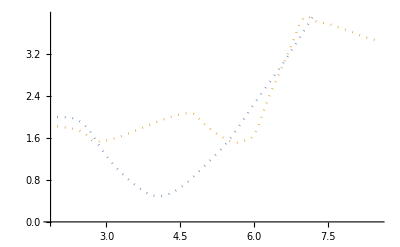

```mathematica
Show[ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λmh1[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λph1[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dotted],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dotted],InterpolationOrder->2]]
```

#### harmonic2

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.hsubs2/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.hsubs2/.ωd->freq0];
ord1=OrderingBy[evalsbase,Abs[#]&][[1;;4]];
ord2=OrderingBy[evalsbase2,Abs[#]&][[1;;4]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{835.222+0.00343876 ⅈ,835.222-0.00343876 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.hsubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.hsubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{171.684,Null}

{24.0034,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
v=rev[[All,ind1]];
w=lev[[All,ind2]];
Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,das,asmax,das}]
```

{18.9618,Null}{2.92743,Null}

1 835.222+0.00343876 ⅈ 38.697 6.25303

2 837.699-0.0107983 ⅈ 6.15262×10^-6 0.0300609

3 837.698-0.0107985 ⅈ 9.75907×10^-11 6.71968×10^-7

4 837.698-0.0107985 ⅈ 4.75886×10^-16 6.77947×10^-11

5 837.698-0.0107985 ⅈ 7.77241×10^-16 1.49417×10^-10

6 837.698-0.0107985 ⅈ 3.00068×10^-16 1.72078×10^-10

7 837.698-0.0107985 ⅈ 4.27004×10^-16 1.06647×10^-10

8 837.698-0.0107985 ⅈ 7.34709×10^-16 3.11245×10^-10

9 837.698-0.0107985 ⅈ 3.86797×10^-16 2.23075×10^-10

10 837.698-0.0107985 ⅈ 8.57461×10^-16 1.4923×10^-10

{18.9692,Null}{2.85538,Null}

1 869.884+0.00893023 ⅈ 0.0049933 30.7427

2 871.67+0.00371267 ⅈ 0.0000243636 0.184552

3 871.46+0.00465187 ⅈ 1.20638×10^-7 0.00115725

4 871.46+0.00465172 ⅈ 2.04451×10^-14 3.1122×10^-10

5 871.46+0.00465172 ⅈ 1.08952×10^-14 3.5029×10^-10

6 871.46+0.00465172 ⅈ 1.06027×10^-14 2.47105×10^-10

7 871.46+0.00465172 ⅈ 1.12394×10^-14 1.45121×10^-10

8 871.46+0.00465172 ⅈ 1.26843×10^-14 4.85306×10^-10

9 871.46+0.00465172 ⅈ 6.89604×10^-15 2.86938×10^-10

10 871.46+0.00465172 ⅈ 1.45336×10^-14 2.79702×10^-10

{19.2651,Null}{2.82633,Null}

1 874.916+0.000369401 ⅈ 0.00580171 6.44787

2 880.188-0.000690875 ⅈ 8.9712×10^-6 0.0429731

3 880.21-0.000706898 ⅈ 2.70414×10^-9 7.39553×10^-6

4 880.21-0.000706898 ⅈ 7.35957×10^-15 1.61495×10^-10

5 880.21-0.000706898 ⅈ 4.4431×10^-15 4.46989×10^-10

6 880.21-0.000706898 ⅈ 3.43652×10^-15 5.98917×10^-11

7 880.21-0.000706898 ⅈ 8.50043×10^-15 2.77211×10^-10

8 880.21-0.000706898 ⅈ 3.80885×10^-15 2.12124×10^-10

9 880.21-0.000706898 ⅈ 6.92795×10^-15 3.28271×10^-10

10 880.21-0.000706898 ⅈ 1.20492×10^-14 2.01801×10^-10

{19.7438,Null}{2.8539,Null}

1 895.161-0.00745156 ⅈ 0.00650203 3.67908

2 899.957-0.00736791 ⅈ 4.3615×10^-6 0.0242562

3 899.968-0.00736502 ⅈ 6.17122×10^-10 2.8329×10^-6

4 899.968-0.00736502 ⅈ 1.1122×10^-14 2.9941×10^-10

5 899.968-0.00736502 ⅈ 7.76924×10^-15 5.33357×10^-10

6 899.968-0.00736502 ⅈ 7.3097×10^-15 2.0217×10^-10

7 899.968-0.00736502 ⅈ 4.96155×10^-15 2.36032×10^-10

8 899.968-0.00736502 ⅈ 1.089×10^-14 1.08023×10^-10

9 899.968-0.00736502 ⅈ 5.69729×10^-15 2.01569×10^-10

10 899.968-0.00736502 ⅈ 2.26036×10^-15 1.20919×10^-10

{21.1013,Null}{2.86654,Null}

1 924.043-0.0140332 ⅈ 0.00668327 3.41437

2 926.587-0.0130539 ⅈ 1.02645×10^-6 0.00800021

3 926.588-0.0130529 ⅈ 6.78734×10^-12 3.38398×10^-8

4 926.588-0.0130529 ⅈ 7.74301×10^-15 5.99625×10^-9

5 926.588-0.0130529 ⅈ 6.59203×10^-15 6.1597×10^-9

6 926.588-0.0130529 ⅈ 7.35675×10^-15 1.58573×10^-9

7 926.588-0.0130529 ⅈ 8.39125×10^-16 6.05393×10^-9

8 926.588-0.0130529 ⅈ 1.08019×10^-14 4.71514×10^-9

9 926.588-0.0130529 ⅈ 3.58996×10^-15 2.48723×10^-9

10 926.588-0.0130529 ⅈ 1.0179×10^-14 4.74463×10^-9

{20.5278,Null}{2.86029,Null}

1 954.941-0.0180015 ⅈ 0.00660293 3.30546

2 956.201-0.0166502 ⅈ 2.63852×10^-7 0.00274723

3 956.201-0.0166502 ⅈ 2.12936×10^-14 4.88373×10^-9

4 956.201-0.0166502 ⅈ 6.6696×10^-15 5.684×10^-9

5 956.201-0.0166502 ⅈ 5.28875×10^-15 3.08624×10^-9

6 956.201-0.0166502 ⅈ 3.53944×10^-15 6.49454×10^-10

7 956.201-0.0166502 ⅈ 6.38924×10^-15 3.92494×10^-9

8 956.201-0.0166502 ⅈ 4.37861×10^-15 4.43663×10^-9

9 956.201-0.0166502 ⅈ 4.30428×10^-15 5.34378×10^-9

10 956.201-0.0166502 ⅈ 3.77048×10^-15 1.26843×10^-9

{21.6044,Null}{2.86968,Null}

1 986.047-0.0191927 ⅈ 0.0061947 3.11797

2 987.274-0.0181468 ⅈ 1.66352×10^-7 0.00219024

3 987.274-0.0181468 ⅈ 3.94827×10^-14 1.59883×10^-9

4 987.274-0.0181468 ⅈ 3.80316×10^-15 6.31312×10^-9

5 987.274-0.0181468 ⅈ 1.32759×10^-14 6.98855×10^-9

6 987.274-0.0181468 ⅈ 2.06944×10^-15 3.00179×10^-9

7 987.274-0.0181468 ⅈ 3.64512×10^-15 4.43926×10^-9

8 987.274-0.0181468 ⅈ 1.52029×10^-14 1.80275×10^-9

9 987.274-0.0181468 ⅈ 1.35675×10^-14 3.15178×10^-9

10 987.274-0.0181468 ⅈ 5.68605×10^-15 3.02381×10^-9

{20.1788,Null}{2.8457,Null}

1 1018.44-0.0189278 ⅈ 0.00503597 2.87502

2 1021.01-0.0185999 ⅈ 2.13995×10^-7 0.00529357

3 1021.01-0.0185998 ⅈ 1.243×10^-13 1.00166×10^-8

4 1021.01-0.0185998 ⅈ 8.77306×10^-15 1.02379×10^-8

5 1021.01-0.0185998 ⅈ 3.31011×10^-15 6.86604×10^-9

6 1021.01-0.0185998 ⅈ 2.64431×10^-15 2.99472×10^-10

7 1021.01-0.0185998 ⅈ 7.41238×10^-15 2.76331×10^-9

8 1021.01-0.0185998 ⅈ 3.52903×10^-15 6.253×10^-9

9 1021.01-0.0185998 ⅈ 6.5929×10^-15 4.61367×10^-9

10 1021.01-0.0185998 ⅈ 3.94794×10^-15 3.3042×10^-9

{20.2756,Null}{2.87946,Null}

1 1056.07-0.0187013 ⅈ 0.00323626 2.65912

2 1061.49-0.0184906 ⅈ 2.92826×10^-7 0.015226

3 1061.49-0.0184903 ⅈ 4.37982×10^-13 4.613×10^-8

4 1061.49-0.0184903 ⅈ 5.79894×10^-15 1.00827×10^-8

5 1061.49-0.0184903 ⅈ 3.62454×10^-15 6.749×10^-9

6 1061.49-0.0184903 ⅈ 3.37512×10^-15 6.5672×10^-9

7 1061.49-0.0184903 ⅈ 2.50071×10^-15 1.14365×10^-8

8 1061.49-0.0184903 ⅈ 1.21188×10^-15 4.69744×10^-9

9 1061.49-0.0184903 ⅈ 6.34601×10^-15 7.16649×10^-9

10 1061.49-0.0184903 ⅈ 5.71639×10^-15 8.49331×10^-9

{22.7842,Null}{2.85553,Null}

1 1106.2-0.0177055 ⅈ 0.00174393 2.51316

2 1117.6-0.0168391 ⅈ 4.93239×10^-7 0.0440439

3 1117.61-0.0168363 ⅈ 4.49513×10^-11 5.04035×10^-6

4 1117.61-0.0168363 ⅈ 2.66273×10^-15 2.16092×10^-8

5 1117.61-0.0168363 ⅈ 1.43154×10^-15 9.41999×10^-9

6 1117.61-0.0168363 ⅈ 3.66173×10^-15 1.31697×10^-8

7 1117.61-0.0168363 ⅈ 2.85582×10^-15 2.20506×10^-8

8 1117.61-0.0168363 ⅈ 3.99731×10^-15 2.60986×10^-8

9 1117.61-0.0168363 ⅈ 4.87774×10^-15 9.19414×10^-9

10 1117.61-0.0168363 ⅈ 2.77606×10^-15 1.57977×10^-8

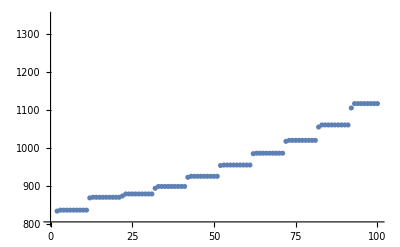

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λph2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λph2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{20.5178,Null}{2.86907,Null}

1 1117.61-0.0168363 ⅈ 2.75058×10^-15 1.58166×10^-8

2 1117.61-0.0168363 ⅈ 2.09558×10^-15 1.077×10^-8

3 1117.61-0.0168363 ⅈ 3.01361×10^-15 2.26376×10^-8

4 1117.61-0.0168363 ⅈ 9.9663×10^-16 3.76612×10^-9

5 1117.61-0.0168363 ⅈ 5.57409×10^-15 2.35686×10^-8

6 1117.61-0.0168363 ⅈ 2.63133×10^-15 1.03841×10^-8

7 1117.61-0.0168363 ⅈ 2.49153×10^-15 9.64487×10^-9

8 1117.61-0.0168363 ⅈ 1.63777×10^-15 1.40443×10^-8

9 1117.61-0.0168363 ⅈ 5.13977×10^-15 2.197×10^-8

10 1117.61-0.0168363 ⅈ 5.94151×10^-15 1.0175×10^-8

{20.5961,Null}{2.85161,Null}

1 1767.96+0.123478 ⅈ 0.000209221 83.7951

2 1886.79+0.0868033 ⅈ 0.000229441 5.32563

3 1852.26+0.00122448 ⅈ 3.24378×10^-6 0.804419

4 1852.54-0.00383824 ⅈ 4.00962×10^-9 0.00107252

5 1852.54-0.00383832 ⅈ 4.08038×10^-15 2.05581×10^-8

6 1852.54-0.00383832 ⅈ 2.66116×10^-15 3.03919×10^-8

7 1852.54-0.00383832 ⅈ 1.82952×10^-15 5.92067×10^-8

8 1852.54-0.00383832 ⅈ 2.41528×10^-15 1.04358×10^-7

9 1852.54-0.00383832 ⅈ 1.34168×10^-15 3.01121×10^-8

10 1852.54-0.00383832 ⅈ 1.36603×10^-15 4.26487×10^-8

{20.6241,Null}{2.85785,Null}

1 2957.68+0.0297982 ⅈ 0.000194267 328.716

2 3075.75-0.468661 ⅈ 0.0000430991 3.95968

3 3060.78+0.156165 ⅈ 2.73175×10^-6 0.554138

4 3063.57-0.0115311 ⅈ 4.31302×10^-7 0.0560642

5 3063.53-0.00399736 ⅈ 8.52552×10^-10 0.000110684

6 3063.53-0.00399727 ⅈ 1.00866×10^-15 1.01712×10^-6

7 3063.53-0.00399727 ⅈ 4.66886×10^-15 6.50667×10^-7

8 3063.53-0.00399727 ⅈ 4.77872×10^-15 8.56905×10^-7

9 3063.53-0.00399727 ⅈ 4.51725×10^-15 1.80186×10^-7

10 3063.53-0.00399727 ⅈ 2.2187×10^-15 8.57259×10^-7

{21.2894,Null}{2.88522,Null}

1 3684.86+0.0153027 ⅈ 0.000256777 2139.98

2 4020.51-0.016794 ⅈ 0.000176985 41.1754

3 4209.98-0.0405333 ⅈ 0.0000888973 10.1701

4 4212.96-0.00138686 ⅈ 1.64589×10^-6 0.0332845

5 4212.96-0.0014321 ⅈ 2.22688×10^-11 2.96781×10^-7

6 4212.96-0.0014321 ⅈ 9.69844×10^-16 7.58806×10^-8

7 4212.96-0.0014321 ⅈ 9.22882×10^-16 4.50881×10^-8

8 4212.96-0.0014321 ⅈ 9.66923×10^-16 3.80493×10^-8

9 4212.96-0.0014321 ⅈ 9.72135×10^-16 3.78788×10^-8

10 4212.96-0.0014321 ⅈ 7.80323×10^-16 5.19533×10^-8

{21.011,Null}{2.85565,Null}

1 5471.91-0.041465 ⅈ 0.00030595 978.848

2 5418.29-0.00413062 ⅈ 4.87785×10^-6 0.446778

3 5417.19+0.00170349 ⅈ 6.9567×10^-8 0.00368231

4 5417.19+0.00169498 ⅈ 1.06617×10^-12 6.52203×10^-8

5 5417.19+0.00169498 ⅈ 1.12826×10^-15 5.13724×10^-9

6 5417.19+0.00169498 ⅈ 1.36344×10^-15 5.07986×10^-9

7 5417.19+0.00169498 ⅈ 8.8647×10^-16 3.47795×10^-9

8 5417.19+0.00169498 ⅈ 7.66903×10^-16 6.11732×10^-9

9 5417.19+0.00169498 ⅈ 1.06945×10^-15 1.32602×10^-9

10 5417.19+0.00169498 ⅈ 8.39019×10^-16 1.17935×10^-9

{22.3982,Null}{2.84872,Null}

1 6671.76+0.0170965 ⅈ 0.000239034 1814.74

2 6682.53-0.0000650041 ⅈ 2.24861×10^-6 0.0344457

3 6682.53-0.0000680652 ⅈ 2.61966×10^-12 6.39267×10^-8

4 6682.53-0.0000680652 ⅈ 1.57403×10^-15 9.07633×10^-9

5 6682.53-0.0000680652 ⅈ 1.19657×10^-15 1.29511×10^-8

6 6682.53-0.0000680652 ⅈ 2.15953×10^-15 5.64093×10^-9

7 6682.53-0.0000680652 ⅈ 9.13721×10^-16 5.96201×10^-9

8 6682.53-0.0000680652 ⅈ 1.81151×10^-15 1.02086×10^-8

9 6682.53-0.0000680652 ⅈ 1.14432×10^-15 4.19423×10^-9

10 6682.53-0.0000680652 ⅈ 9.44614×10^-16 1.52442×10^-8

{20.7102,Null}{2.85677,Null}

1 8007.72-0.000883215 ⅈ 0.000295317 1660.61

2 8010.69-0.000900586 ⅈ 3.15103×10^-7 0.0100068

3 8010.68-0.000900776 ⅈ 3.75442×10^-11 1.28514×10^-6

4 8010.68-0.000900776 ⅈ 1.83507×10^-15 3.2293×10^-8

5 8010.68-0.000900776 ⅈ 1.34463×10^-15 2.26181×10^-8

6 8010.68-0.000900776 ⅈ 1.05989×10^-15 3.83629×10^-8

7 8010.68-0.000900776 ⅈ 5.89312×10^-16 1.67416×10^-8

8 8010.68-0.000900776 ⅈ 1.37605×10^-15 4.13275×10^-8

9 8010.68-0.000900776 ⅈ 2.17741×10^-15 1.68508×10^-8

10 8010.68-0.000900776 ⅈ 2.16342×10^-15 5.14102×10^-8

{23.2058,Null}{2.86097,Null}

1 9426.02-0.00532291 ⅈ 0.00027526 3470.3

2 8921.72-18.3574 ⅈ 0.0000477345 4.48143

3 9241.62-6.17434 ⅈ 0.0000175582 1.46178

4 9341.74-10.3205 ⅈ 8.027×10^-6 0.861996

5 9402.71-9.53328 ⅈ 0.000010115 0.242983

6 9411.89-3.90703 ⅈ 1.32544×10^-6 0.440543

7 9392.49-2.77085 ⅈ 6.87555×10^-7 0.560997

8 9396.64+0.0824603 ⅈ 5.72673×10^-8 0.0676903

9 9396.62-0.000962885 ⅈ 1.83463×10^-10 0.000193684

10 9396.62-0.000963054 ⅈ 1.8858×10^-15 1.87122×10^-6

{20.8756,Null}{2.86557,Null}

1 9011.07-0.11451 ⅈ 0.000106875 21409.1

2 9023.13-0.049742 ⅈ 1.04509×10^-6 0.250599

3 9026.04+0.273321 ⅈ 9.68681×10^-8 0.0217099

4 9026.05+0.277329 ⅈ 2.15554×10^-11 0.0000136332

5 9026.05+0.277329 ⅈ 5.60951×10^-15 0.0000119221

6 9026.05+0.277329 ⅈ 9.02244×10^-15 0.0000241374

7 9026.05+0.277329 ⅈ 2.4981×10^-15 7.26104×10^-6

8 9026.05+0.277329 ⅈ 7.73304×10^-15 0.0000125216

9 9026.05+0.277329 ⅈ 1.20123×10^-14 9.39072×10^-6

10 9026.05+0.277329 ⅈ 1.63562×10^-15 2.60415×10^-6

{21.561,Null}{2.9284,Null}

1 9382.93+16.8114 ⅈ 0.0000392065 29140.3

2 8867.02+16.9319 ⅈ 0.0000427604 23.8475

3 8709.33-3.6865 ⅈ 0.0000131722 5.25845

4 8722.01-11.116 ⅈ 5.05099×10^-6 3.79651

5 8756.79-9.94718 ⅈ 0.0000108451 1.92731

6 8762.25+0.0220585 ⅈ 3.79151×10^-6 0.179459

7 8762.17+0.000270962 ⅈ 2.42217×10^-9 0.000121888

8 8762.17+0.000270946 ⅈ 8.71034×10^-16 1.22859×10^-6

9 8762.17+0.000270946 ⅈ 1.03499×10^-15 9.62898×10^-7

10 8762.17+0.000270946 ⅈ 1.02167×10^-15 2.13798×10^-6

{23.2909,Null}{2.8602,Null}

1 8385.46-0.00154789 ⅈ 0.0000799777 79190.4

2 8385.58-0.00207116 ⅈ 2.25796×10^-8 0.0058245

3 8385.58-0.00207093 ⅈ 2.01908×10^-15 9.40169×10^-6

4 8385.58-0.00207093 ⅈ 1.31146×10^-15 4.31473×10^-6

5 8385.58-0.00207093 ⅈ 1.95075×10^-15 2.70691×10^-6

6 8385.58-0.00207093 ⅈ 1.74318×10^-15 4.46267×10^-6

7 8385.58-0.00207093 ⅈ 1.64642×10^-15 6.59207×10^-6

8 8385.58-0.00207093 ⅈ 9.232×10^-16 4.38999×10^-6

9 8385.58-0.00207093 ⅈ 7.79772×10^-16 4.80482×10^-6

10 8385.58-0.00207093 ⅈ 1.28554×10^-15 2.53358×10^-6

{627.183,Null}

```mathematica
w=w0;
v=v0;
λmh2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λmh2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{26.7978,Null}{2.94697,Null}

1 1117.61-0.0168363 ⅈ 2.75058×10^-15 1.58166×10^-8

2 1117.61-0.0168363 ⅈ 2.09558×10^-15 1.077×10^-8

3 1117.61-0.0168363 ⅈ 3.01361×10^-15 2.26376×10^-8

4 1117.61-0.0168363 ⅈ 9.9663×10^-16 3.76612×10^-9

5 1117.61-0.0168363 ⅈ 5.57409×10^-15 2.35686×10^-8

6 1117.61-0.0168363 ⅈ 2.63133×10^-15 1.03841×10^-8

7 1117.61-0.0168363 ⅈ 2.49153×10^-15 9.64487×10^-9

8 1117.61-0.0168363 ⅈ 1.63777×10^-15 1.40443×10^-8

9 1117.61-0.0168363 ⅈ 5.13977×10^-15 2.197×10^-8

10 1117.61-0.0168363 ⅈ 5.94151×10^-15 1.0175×10^-8

{28.3189,Null}{5.58624,Null}

1 467.55+0.025468 ⅈ 0.000209575 28.0118

2 656.191-0.0723147 ⅈ 0.0000128913 9.69948

3 573.296-0.0400535 ⅈ 1.85804×10^-6 1.19247

4 571.617-0.0400311 ⅈ 7.23512×10^-9 0.00326795

5 571.617-0.0400311 ⅈ 4.63771×10^-15 3.18994×10^-8

6 571.617-0.0400311 ⅈ 4.26771×10^-15 1.44076×10^-8

7 571.617-0.0400311 ⅈ 6.71003×10^-15 4.67854×10^-8

8 571.617-0.0400311 ⅈ 7.38387×10^-15 3.9065×10^-8

9 571.617-0.0400311 ⅈ 1.34433×10^-14 9.45789×10^-9

10 571.617-0.0400311 ⅈ 7.70846×10^-15 2.83955×10^-8

{24.8037,Null}{2.93308,Null}

1 841.212-0.563012 ⅈ 0.000177393 12.8894

2 1080.68+3.38824 ⅈ 0.00017817 11.9725

3 3386.56+169.653 ⅈ 0.000280108 82.4399

4 876.204+60.7275 ⅈ 0.000102 24.1446

5 1221.39+1024.69 ⅈ 0.000289331 33.8263

6 281.886+49.0886 ⅈ 0.000122516 27.3145

7 629.915+324.768 ⅈ 0.0000825558 20.9575

8 906.837+328.925 ⅈ 0.0000613408 9.25917

9 801.769+245.5 ⅈ 0.0000588324 4.76916

10 821.716+217.786 ⅈ 0.0000139424 1.38789

{22.3984,Null}{2.87026,Null}

1 1598.-43.4802 ⅈ 0.000275508 180.18

2 1385.57+88.0756 ⅈ 0.0000492544 4.26643

3 1380.07+92.58 ⅈ 4.2098×10^-7 0.0993313

4 1380.09+92.5589 ⅈ 1.31229×10^-10 0.0000343731

5 1380.09+92.5589 ⅈ 1.28636×10^-15 1.61743×10^-8

6 1380.09+92.5589 ⅈ 1.12372×10^-15 4.75836×10^-8

7 1380.09+92.5589 ⅈ 1.34859×10^-15 1.06589×10^-8

8 1380.09+92.5589 ⅈ 1.06481×10^-15 2.00371×10^-8

9 1380.09+92.5589 ⅈ 1.08227×10^-15 7.06069×10^-8

10 1380.09+92.5589 ⅈ 8.1555×10^-16 1.36473×10^-8

{22.5207,Null}{3.06194,Null}

1 1747.94+18.2932 ⅈ 0.000237305 80.5923

2 1765.88+1.461 ⅈ 2.80714×10^-6 1.88174

3 1762.33-0.000791332 ⅈ 9.5099×10^-8 0.0576007

4 1762.32-6.2864×10^-6 ⅈ 1.54561×10^-12 1.47111×10^-6

5 1762.32-6.2864×10^-6 ⅈ 1.02746×10^-15 3.72173×10^-8

6 1762.32-6.2864×10^-6 ⅈ 1.05301×10^-15 2.41417×10^-8

7 1762.32-6.2864×10^-6 ⅈ 9.58092×10^-16 5.86468×10^-9

8 1762.32-6.28638×10^-6 ⅈ 1.2467×10^-15 2.4269×10^-8

9 1762.32-6.28639×10^-6 ⅈ 1.19843×10^-15 3.26577×10^-8

10 1762.32-6.28635×10^-6 ⅈ 1.08935×10^-15 2.49983×10^-8

{22.7102,Null}{2.92963,Null}

1 2084.26-0.000704262 ⅈ 0.000227659 40.7516

2 2035.85+0.000607377 ⅈ 0.0000148925 0.917514

3 2034.82+0.00040053 ⅈ 5.23055×10^-8 0.0100597

4 2034.82+0.000400617 ⅈ 4.10693×10^-14 4.93433×10^-8

5 2034.82+0.000400617 ⅈ 8.70988×10^-16 7.48198×10^-10

6 2034.82+0.000400617 ⅈ 7.53717×10^-16 2.62741×10^-9

7 2034.82+0.000400617 ⅈ 9.40659×10^-16 1.83204×10^-9

8 2034.82+0.000400617 ⅈ 1.01079×10^-15 2.61529×10^-9

9 2034.82+0.000400617 ⅈ 8.89469×10^-16 3.65875×10^-9

10 2034.82+0.000400617 ⅈ 9.88862×10^-16 3.37939×10^-10

{23.0351,Null}{2.93796,Null}

1 2419.8+0.00156097 ⅈ 0.000201868 29.1919

2 2228.1-0.00125043 ⅈ 0.0000420354 3.74168

3 2231.34+6.87195×10^-6 ⅈ 7.16852×10^-7 0.0578044

4 2231.34+0.0000126451 ⅈ 1.33101×10^-11 8.33878×10^-6

5 2231.34+0.0000126451 ⅈ 5.85044×10^-16 1.86429×10^-10

6 2231.34+0.0000126451 ⅈ 6.74622×10^-16 3.49899×10^-10

7 2231.34+0.0000126451 ⅈ 5.60966×10^-16 4.52589×10^-10

8 2231.34+0.0000126451 ⅈ 6.06879×10^-16 2.73604×10^-10

9 2231.34+0.0000126451 ⅈ 5.15822×10^-16 2.90249×10^-10

10 2231.34+0.0000126451 ⅈ 6.28454×10^-16 2.64926×10^-10

{480.985,Null}

#### plot

```mathematica
p0=Show[ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic])/980)),{}]],PlotRange->{{2,10},{0,3}},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Dashed]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Dashed]}],ImageSize->350];
p1=
Show[ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λmh2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λph2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,InterpolationOrder->2,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dashed],InterpolationOrder->2,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λmh1[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λph1[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]]],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],InterpolationOrder->2],PlotRange->{0,3},ImageSize->350];
```

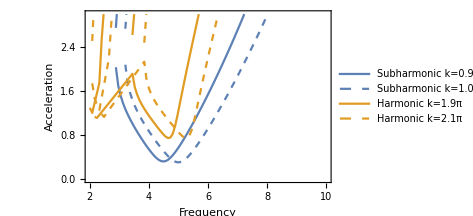
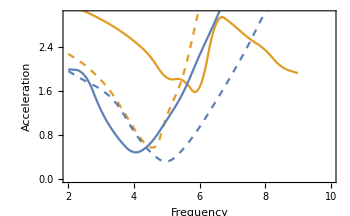
a_s=0 | a_s=0.05
-Graphics- | -Graphics-

```mathematica
p=Legended[Grid[{{Style[DisplayForm[RowBox[{Subscript[a,s],"=","0"}]],16],Style[DisplayForm[RowBox[{Subscript[a,s],"=",asmax}]],16]},{p0,p1}}],LineLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[2]],Dashed]},{"Subharmonic k=0.95π","Subharmonic k=1.05π","Harmonic k=1.9π","Harmonic k=2.1π"}]]
```

```mathematica
Export["boundaries.pdf",p]
```

boundaries.pdf